# MLC

## Mathematica Lattice Code Version 1.8

## Hywel Owen and James Jones This version by Hywel Owen

8th June 2004

## Introduction

### About MLC

MLC is an optics code written completely using core Mathematica commands. It should therefore run on any computer with Mathematica installed. It also has the advantage that it uses the same element and field definitions that MAD does, so the same input file can be alternately run with MLC or Madinput/MAD for comparison.

### Implementation Details

MLC requires the Madinput package, as it uses Madinput to process the element commands and to provide functionality such as splitting elements of MADDraw. It does not require MAD, however.
The MLC commands are defined in the MLC section of the notebook. Examples are given in the section that follows it.

#### Version 1.8

Added new beam distribution commands for alpha<>0.

#### Version 1.7

An option has been added to allow a single-pass correction for non-paraxial transport. The function MLCPropagateNonParaxialRay calculates the retardation to first order of large amplitude particles.

#### Version 1.6

A minor bug in the calculation of phase advances has been fixed. Phase advances greater then π/2 in single elements are now calculated correctly.

#### Version 1.5

Non-relativistic transport has been added. A parameter γ can now be defined and applied to a beamline definition, which defines the reference energy. If this parameter is not given, then γ=∞ is assumed (ultrarelativistic particles)

#### Version 1.3/1.4

Developing cavity matrices - there are a variety of cavity matrix definitions now present, but they have not yet been debugged.

#### Version 1.2

Changed the definitions of R_51, R_52and R_56so that they are consistent with MAD. R_56will now have the opposite sign to before. This is an important change! This now means that the signs are opposite to the TRANSPORT notations.

#### Version 1.1

Fixed a bug in MLCLinearQuadrupoleMatrix so it doesn't cause errors if the quadrupole strength is zero. You can now set zero quardupole strengths (it replaces the element with a drift matrix).

#### Version 1.0

Finally decide to release it as a stable (?) version.
Changed the definition of BPM so you can have non-zero length BPMs as in MAD. These are modelled as drift spaces.

#### Version 0.19

Adds the kick element as a drift space similar to hkick and vkick.

#### Version 0.17

Added Chromaticity Calculations. Some discrepancy between MLC and MAD - could be due to method of integration (MAD only approximates). Also added Beam Size and Beam Angle commands.

#### Version 0.16

Added Momentum Compaction, Energy Loss, Partition Functions, Energy Spread, Emittance and Damping Times.

#### Version 0.15

Added Synchrotron Radiation Integrals 1 - 5

#### Version 0.14

Fixed DPY calculation. Not quite done yet.
Added a beam distribution generator. The truncation only occurs in x and x' planes independently, so it isn't quite right, but will do if the number of sigmas is large.

#### Version 0.13

Modified MLCPlotPeriodicOptics to automatically label and colour plots.

#### Version 0.12

Added a couple of helpful commands, including MLCGeneratePeriodicTwissTable, which means you don't have to find your own Periodic Functions any more, and added MLCPlotPeriodicOptics, which does a standard scaled plot of a system. You still have to use MLCElementList to generate the elements

#### Version 0.11

Minor update to include MLCPropagateRay command, which performs linear ray-tracing through the element system.

#### Version 0.10

First version with everything tested, i.e. phase advances, twiss values in both planes, and horizontal dispersion.

### Known Bugs - Correct up to Version 1.2

Path lengths and R_56terms have been compared with MAD and found to be exactly the same - the R matrices should be considered to be exactly the same as in MAD.
The phase advance through a dipole magnet gives very slightly different values than MAD. This could actually be a truncation error in MAD, since the propagation of phase involves calculating the ArcSin of a small number. For very long elements in which the phase advance is greater than 2 Pi, there could be an error of 2 Pi in the calculated phase advance across this element. This can be solved by slicing the elements up by using MADSplitElements. This could be an issue with other codes, but I'm not sure....
There is a bug in the calculation of DPY; this error occurs in the MLCWedgeBendMagnet element definition.

## Notebook Initialisation

### General Setup

```mathematica
Off[General::"spell1"]
```

```mathematica
Off[General::"spell"]
```

Turns off those annoying messages when you define similar-looking variable names.

```mathematica
Needs["madtomma`madinput`readinmadfiles`"]
```

Version 2.21 of Madtomma`Mfs`Mfs` loaded.  Note function name changes since Version 1.x:
interpretDescriptors→mfsInterpretKeys
keyValue→mfsKeyValue
columnNames→mfsColumnNames
descriptorNames→mfsKeyNames
colValue→mfsColumnValue
addDescriptor→mfsAddKey
editDescriptor→mfsEditKey
deleteDescriptor→mfsDeleteKey
symplecticJ→SymplecticJ

Global`Thin::shdw: Symbol "Thin" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

Needs::nocont: Context "MadtoMMA`MADInput`MADInput`" was not created when Needs was evaluated.

Needs::nocont: Context "madtomma`madinput`readinmadfiles`" was not created when Needs was evaluated.

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

These lines load the other standard packages used in this notebook.

```mathematica
<<"ErrorBarPlots`"
```

```mathematica
<<"PlotLegends`"
```

Legend::shdw: Symbol "Legend" appears in multiple contexts {"PlotLegends`", "Madtomma`MADInput`MADInput`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

### Setup Default File Locations and Scratch Directories

```mathematica
workingdirectory="c:\\mad"
```

c:\mad

```mathematica
SetDirectory[workingdirectory]
```

c:\mad

### Define Useful Parameters

```mathematica
mm=10^-3;mrad=10^-3;
```

```mathematica
Notation[Subscript[k, B] ⟺ BoltzmannConstant]
```

Notation[NotationBoxTag[k_B]⟺NotationBoxTag[BoltzmannConstant]]

```mathematica
Subscript[k, B]
```

k_B

```mathematica
Notation[Subscript[R, g] ⟺ MolarGasConstant]
```

Notation[NotationBoxTag[R_g]⟺NotationBoxTag[MolarGasConstant]]

```mathematica
Subscript[R, g]
```

R_g

### Define Some Useful Functions

```mathematica
ColorQ[x_]:=MemberQ[{RGBColor,GrayLevel,Hue,CMYKColor},Head[x]];
GradientColor[x:{cols__?ColorQ}]:=GradientColor[Transpose[{Range[0,Length[x]-1]/(Length[x]-1),x}]];
GradientColor[x:{{_,_?ColorQ}..}]:=Module[{newx=x,res,redf,greenf,xvals,cols,bluef,func},newx=Sort[x,OrderedQ[{#1⟦1⟧,#2⟦1⟧}]&];If[newx⟦1,1⟧=!=0,PrependTo[newx,{0,newx⟦1,2⟧}]];If[N[Last[newx]⟦1⟧]=!=1.,AppendTo[newx,{1,Last[newx]⟦2⟧}]];{xvals,cols}=Transpose[newx];res=(Transpose[{xvals,#1}]&)/@Transpose[Apply[List,(ToColor[#1,RGBColor]&)/@cols,{1}]];{redf,greenf,bluef}=(Interpolation[#1,InterpolationOrder->1]&)/@res;func=Evaluate[RGBColor[redf[#1],greenf[#1],bluef[#1]]]&;ListDensityPlot[Transpose[Table[{i,i},{i,0,1,0.01}]],Mesh->False,DataRange->{{0,1},{0,1}},Axes->{True,False},Frame->False,AspectRatio->1/10,ColorFunction->func];func];
```

## MLC Version 1.8

#### Package Functions

```mathematica
BeginPackage["MLC`mlc`",{"Madtomma`MADInput`MADInput`","Madtomma`Mfs`Mfs`","Madtomma`Mfs`MAD8Survey`","Notation`","Units`","PhysicalConstants`"}]
```

MLC`mlc`

```mathematica
MLCExtraList::usage="";
```

```mathematica
MLCStripUnusedExtraFields::usage="";
```

```mathematica
MLCElementList::usage="";
```

```mathematica
MLCGetElementLengths::usage="";
```

```mathematica
MLCLinearDriftMatrix::usage="";
```

```mathematica
MLCLinearSextupoleMatrix::usage="";
```

```mathematica
MLCLinearKickerMatrix::usage="";
```

```mathematica
MLCLinearBPMMatrix::usage="";
```

```mathematica
MLCLinearMarkerMatrix::usage="";
```

```mathematica
MLCLinearThickQuadrupoleMatrix::usage="";
```

```mathematica
MLCLinearThinQuadrupoleMatrix::usage="";
```

```mathematica
MLCLinearWedgeBendMatrix::usage="";
```

```mathematica
MLCLinearSolenoidMatrix::usage="";
```

```mathematica
MLCLinearBeamRotationMatrix::usage="";
```

```mathematica
MLCLinearPoleFaceRotationMatrix::usage="";
```

```mathematica
MLCLinearSectorBendMatrix::usage="";
```

```mathematica
MLCLinearRFCCavityMatrix::usage="";
```

```mathematica
MLCLinearCavityMatrix::usage="";
```

```mathematica
MLCLinearRSCavityMatrix::usage="";
```

```mathematica
MLCLinearTRCavityMatrix::usage="";
```

```mathematica
MLCLinearMatrix::usage="";
```

```mathematica
MLCRMatrices::usage="";
```

```mathematica
MLCOneTurnRMatrix::usage="";
```

```mathematica
MLCStability::usage="";
```

```mathematica
MLCFindPeriodicPhase::usage="";
```

```mathematica
MLCFindPeriodicTwiss::usage="";
```

```mathematica
MLCFindPeriodicDispersion::usage="";
```

```mathematica
MLCTwissVectorToMatrix::usage="";
```

```mathematica
MLCTwissMatrixToVector::usage="";
```

```mathematica
MLCGenerateSinglePlaneRMatrices::usage="";
```

```mathematica
MLCPropagateTwissMatrix::usage="";
```

```mathematica
ReverseDot::usage="";
```

```mathematica
MLCCumulativeRMatrices::usage="";
```

```mathematica
MLCReverseCumulativeRMatrices::usage="";
```

```mathematica
MLCPropagateTwissPhaseVector::usage="";
```

```mathematica
MLCTwissOperator::usage="";
```

```mathematica
MLCPropagateTwiss::usage="";
```

```mathematica
MLCPropagateDispersion::usage="";
```

```mathematica
MLCGenerateTwissTable::usage="";
```

```mathematica
MLCGeneratePeriodicTwissTable::usage="";
```

```mathematica
MLCGeneratePeriodicTwissTableNoOut::usage="";
```

```mathematica
MLCPropagateRay::usage="";
```

```mathematica
MLCTwissOperator::usage="";
```

```mathematica
MLCPropagateTwiss::usage="";
```

```mathematica
DotOperator::usage="";
```

```mathematica
MLCRetardNonParaxialRay::usage="";
```

```mathematica
MLCPropagateAndRetardOperator::usage="";
```

```mathematica
MLCPropagateNonParaxialRay::usage="";
```

```mathematica
MLCBetaGamma::usage="";
```

```mathematica
MLCGenerateBeamDistribution6D::usage="";
```

```mathematica
MLCPlot::usage="";
```

```mathematica
MLCPlotPeriodicOptics::usage="";
```

```mathematica
MLCMatrixInspect::usage="";
```

```mathematica
integralSRI1::usage="";
```

```mathematica
MLCSRI1::usage="";
```

```mathematica
SR2Element::usage="";
```

```mathematica
MLCSRI2::usage="";
```

```mathematica
SR3Element::usage="";
```

```mathematica
MLCSRI3::usage="";
```

```mathematica
integralSRI4::usage="";
```

```mathematica
MLCSRI4::usage="";
```

```mathematica
integralSRI5H::usage="";
```

```mathematica
MLCSRI5H::usage="";
```

```mathematica
MLCSRI5::usage="";
```

```mathematica
MLCαc::usage="";
```

```mathematica
MLCϵ::usage="";
```

```mathematica
MLCSRI::usage="";
```

```mathematica
MLCU0::usage="";
```

```mathematica
MLCJx::usage="";
```

```mathematica
MLCJϵ::usage="";
```

```mathematica
MLCES::usage="";
```

```mathematica
MLCτx::usage="";
```

```mathematica
MLCτy::usage="";
```

```mathematica
MLCτϵ::usage="";
```

```mathematica
MLCϵx::usage="";
```

```mathematica
MLCϵy::usage="";
```

```mathematica
MLCσx::usage="";
```

```mathematica
MLCσy::usage="";
```

```mathematica
MLCσprimex::usage="";
```

```mathematica
MLCσprimey::usage="";
```

```mathematica
MLCChromaticity::usage="";
```

```mathematica
MLCGenerateR56::usage="";
```

```mathematica
MLCGenerateR51::usage="";
```

```mathematica
MLCGenerateR52::usage="";
```

```mathematica
MADReadRMatrices::usage="";
```

```mathematica
MADReadTMatrices::usage="";
```

```mathematica
MADGenerateRMatrices::usage="";
```

```mathematica
MLCTransportCompose::usage="";
```

```mathematica
MLCOneTurnRTMatrices::usage="";
```

```mathematica
MLCCumulativeRTMatrices::usage="";
```

```mathematica
MLCTransport::usage="";
```

```mathematica
MLCElems::usage="";
MLCS::usage="";
MLCBETX::usage="";
MLCALFX::usage="";
MLCGAMX::usage="";
MLCBETY::usage="";
MLCALFY::usage="";
MLCGAMY::usage="";
MLCMUX::usage="";
MLCMUY::usage="";
MLCDX::usage="";
MLCDPX::usage="";
MLCDY::usage="";
MLCDPY::usage="";
```

```mathematica
Begin["`Private`"]
```

MLC`mlc`Private`

#### Distribution Functions

TruncatedGaussianSample creates a sample drawn from a Gaussian Distribution of mean μ and s.d. σ which is truncated at n sigma

```mathematica
TruncatedGaussianSample[mean_,sigma_,n_]:=(
While[Abs[(a=RandomReal[NormalDistribution[mean,sigma]])-mean]>(n*sigma)];a)
```

```mathematica
TruncatedGaussianSample[mean_,0,n_]:=(
mean)
```

```mathematica
TruncatedGaussianSample[mean_,0.,n_]:=(
mean)
```

GaussianEnsemble creates a set of such samples

```mathematica
GaussianEnsemble[nparticles_,nmean_,nsigma_,ntruncation_]:=Table[TruncatedGaussianSample[nmean,nsigma,ntruncation],{nparticles}];
```

UniformEnsemble creates a set of samples drawn from a Uniform (rectangular) distribution between nmin and nmax

```mathematica
UniformEnsemble[nparticles_,nmin_,nmax_]:=Table[Random[UniformDistribution[nmin,nmax]],{nparticles}];
```

UniformEnsemble creates a set of samples drawn from a Uniform (rectangular) distribution between nmin and nmax

Mathematica includess a command which shows how to get the standard deviation of a uniform sample. This is simply:

```mathematica
StandardDeviation[UniformDistribution[{xmin,xmax}]]
```

(xmax-xmin)/(2 √3)

#### Process Commands

```mathematica
MLCExtraList[lattice_]:=ToExpression[(#<>"Extra")&/@(Transpose[MADFlatten[lattice]][[1]])]
```

```mathematica
MLCStripUnusedExtraFields[extralist_]:=Drop[#,2]&/@extralist
```

```mathematica
MLCElementList[lattice_]:=Join[#[[1]],#[[2]]]&/@Transpose[{MADFlatten[lattice],MLCStripUnusedExtraFields[MLCExtraList[lattice]]}]
```

```mathematica
MLCGetElementLengths[lattice_]:=(MADFlatten[lattice]//Transpose)[[3]]
```

#### Matrix Element Definitions

```mathematica
MLCLinearDriftMatrix[elem_,γ_:Infinity]:=Module[{L,β},L=elem[[3]];β=√(1-1/γ^2);
({{1, L, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, L, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, L/(β^2 γ^2)}, {0, 0, 0, 0, 0, 1}})]
```

```mathematica
MLCLinearSextupoleMatrix[elem_,γ_:Infinity]:=MLCLinearDriftMatrix[elem,γ]
```

```mathematica
MLCLinearKickerMatrix[elem_,γ_:Infinity]:=MLCLinearDriftMatrix[elem,γ]
```

```mathematica
MLCLinearBPMMatrix[elem_,γ_:Infinity]:=MLCLinearDriftMatrix[elem,γ]
```

```mathematica
MLCLinearMarkerMatrix[elem_,γ_:Infinity]:=IdentityMatrix[6]
```

```mathematica
(*MLCLinearThickQuadrupoleMatrix[elem_,γ_:Infinity]:=Module[{L,k},L=elem[[3]];k=Sqrt[elem[[4]]];If[Positive[elem[[4]]],k=Sqrt[elem[[4]]];{{Cos[k L],Sin[k L]/k,0,0,0,0},{-k Sin[k L],Cos[k L],0,0,0,0},{0,0,Cosh[k L],Sinh[k L]/k,0,0},{0,0,k Sinh[k L],Cosh[k L],0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},k=Sqrt[-elem[[4]]];{{Cosh[k L],Sinh[k L]/k,0,0,0,0},{k Sinh[k L],Cosh[k L],0,0,0,0},{0,0,Cos[k L],Sin[k L]/k,0,0},{0,0,-k Sin[k L],Cos[k L],0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]]*)
```

```mathematica
MLCLinearThickQuadrupoleMatrix[elem_,γ_:Infinity]:=Module[{L,k,β},L=elem[[3]];k=Sqrt[elem[[4]]];β=√(1-1/γ^2);Switch[elem[[4]],_?Positive,k=Sqrt[elem[[4]]];({{Cos[k L], Sin[k L]/k, 0, 0, 0, 0}, {-k Sin[k L], Cos[k L], 0, 0, 0, 0}, {0, 0, Cosh[k L], Sinh[k L]/k, 0, 0}, {0, 0, k Sinh[k L], Cosh[k L], 0, 0}, {0, 0, 0, 0, 1, L/(β^2 γ^2)}, {0, 0, 0, 0, 0, 1}}),_?Negative,k=Sqrt[-elem[[4]]];({{Cosh[k L], Sinh[k L]/k, 0, 0, 0, 0}, {k Sinh[k L], Cosh[k L], 0, 0, 0, 0}, {0, 0, Cos[k L], Sin[k L]/k, 0, 0}, {0, 0, -k Sin[k L], Cos[k L], 0, 0}, {0, 0, 0, 0, 1, L/(β^2 γ^2)}, {0, 0, 0, 0, 0, 1}}),_,MLCLinearDriftMatrix[elem,γ]]]
```

```mathematica
MLCLinearThinQuadrupoleMatrix[elem_]:=Module[{L,k},L=elem[[3]];k=Sqrt[Abs[elem[[4]]]];{{1,0,0,0,0,0},{If[Positive[elem[[4]]],-k Sin[k L],k Sinh[k L]],1,0,0,0,0},{0,0,1,0,0,0},{0,0,If[k>0,k Sinh[k L],-k Sin[k L]],1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

```mathematica
MLCLinearWedgeBendMatrix[elem_,γ_:Infinity]:=Module[{L,kx,ky,ρ, h, n,β},L=elem[[3]];ρ=L/elem[[6]];n=-elem[[4]] ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];β=√(1-1/γ^2);
{{Cos[kx L],If[kx==0,L,Sin[kx L]/kx],0,0,0,If[kx==0,(h L^2)/(2 β),(h (1-Cos[kx L]))/(β kx^2)]},{-kx Sin[kx L],Cos[kx L],0,0,0,If[kx==0,(h L)/β,(h Sin[kx L])/(β kx)]},{0,0,Cos[ky L],If[ky==0,L,Sin[ky L]/ky],0,0},{0,0,-ky Sin[ky L],Cos[ky L],0,0},{If[kx==0,-(h L)/β,-(h Sin[kx L])/(β kx)],If[kx==0,-(h L^2)/(2 β),-(h (1-Cos[kx L]))/(β kx^2)],0,0,1,If[kx==0,L/(β^2 γ^2)-(h^2 L^3)/(6 β^2),L/(β^2 γ^2)-(h^2 (kx L-Sin[kx L]))/(β^2 kx^3)]},{0,0,0,0,0,1}}]
```

```mathematica
MLCLinearSolenoidMatrix[elem_]:=Module[{L,K,Cval,Sval},L=elem[[1]];K=elem[[2]];Cval=Cos [K L];Sval=Sin[K L];
{{Cval,Sval/K,0,0,0,0},{-K Sval,Cval,0,0,0,0},{0,0,Cval,Sval/K,0,0},{0,0,-K Sval,Cval,0,0},{0,0,0,0,1,0},{0,0,0,0,1,1}}]
```

```mathematica
MLCLinearBeamRotationMatrix[α_]:={{Cos[α],0,Sin[α],0,0,0},{0,Cos[α],0,Sin[α],0,0},{-Sin[α],0,Cos[α],0,0,0},{0,-Sin[α],0,Cos[α],0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}
```

```mathematica
MLCLinearPoleFaceRotationMatrix[β_,ρ_,k_,gap_]:=Module[{φ,h},h=1/ρ;φ=k h gap(1+Sin[β]^2)/Cos[β];{{1,0,0,0,0,0},{h Tan[β],1,0,0,0,0},{0,0,1,0,0,0},{0,0,-h Tan[β-φ],1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

```mathematica
MLCLinearSectorBendMatrix[elem_,γ_:Infinity]:=Module[{beta1,beta2,L,ρ,k,gap,β},L=elem[[3]];ρ=L/elem[[6]];k=elem[[4]];beta1=elem[[10]];beta2=elem[[11]];β=√(1-1/γ^2);Chop[MLCLinearPoleFaceRotationMatrix[beta2,ρ,k,0.0].MLCLinearWedgeBendMatrix[elem,γ].MLCLinearPoleFaceRotationMatrix[beta1,ρ,k,0.0]]]
```

```mathematica
MLCLinearRFCCavityMatrix[elem_]:=Module[{L,dE,ϕ,λ,E0},Print["1"];L=elem[[3]];dE=elem[[10]];ϕ=elem[[11]];λ=elem[[12]];E0=elem[[14]];
({{1, If[dE==0,L,L E0/(dE  Cos[ϕ])Log[1+(dE Cos[ϕ])/E0]], 0, 0, 0, 0}, {0, E0/(E0+dE Cos[ϕ]), 0, 0, 0, 0}, {0, 0, 1, If[dE==0,L,L E0/(dE  Cos[ϕ])Log[1+(dE Cos[ϕ])/E0]], 0, 0}, {0, 0, 0, E0/(E0+dE Cos[ϕ]), 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, (dE Sin[ϕ])/(E0+dE Cos[ϕ])(2π)/λ, E0/(E0+dE Cos[ϕ])}})]
```

Linear Cavity with no focusing:

```mathematica
MLCLinearCavityMatrix[elem_]:=Module[{L,dE,ϕ,λ,E0},Print["2"];L=elem[[3]];dE=elem[[10]];ϕ=elem[[11]];λ=(2.99792458 10^2)/elem[[12]];E0=elem[[20]];
({{1, If[dE==0,L,L E0/(dE  Cos[ϕ])Log[1+(dE Cos[ϕ])/E0]], 0, 0, 0, 0}, {0, E0/(E0+dE Cos[ϕ]), 0, 0, 0, 0}, {0, 0, 1, If[dE==0,L,L E0/(dE  Cos[ϕ])Log[1+(dE Cos[ϕ])/E0]], 0, 0}, {0, 0, 0, E0/(E0+dE Cos[ϕ]), 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, (dE Sin[ϕ])/(E0+dE Cos[ϕ])(2π)/λ, E0/(E0+dE Cos[ϕ])}})]
```

Rosenzweig-Serafini definition of cavity matrix:

```mathematica
MLCLinearRSCavityMatrix[elem_]:=Module[{L,dE,ϕ,λ,E0,αf},L=elem[[3]];dE=elem[[10]];ϕ=elem[[11]];λ=(2.99792458 10^2)/elem[[12]];E0=elem[[20]];αf=1/(√8 Cos[ϕ])Log[1+(dE Cos[ϕ])/E0];
If[dE==0,MLCLinearDriftMatrix[elem],
({{Cos[αf]-√2 Cos[ϕ]Sin[αf], √8 E0/(dE Cos[ϕ])Cos[ϕ]Sin[αf], 0, 0, 0, 0}, {-(dE Cos[ϕ])/E0(Cos[ϕ]/(√2)+1/(√8 Cos[ϕ]))Sin[αf], E0/(E0+dE Cos[ϕ])(Cos[αf]+√2 Cos[ϕ]Sin[αf]), 0, 0, 0, 0}, {0, 0, Cos[αf]-√2 Cos[ϕ]Sin[αf], √8 E0/(dE Cos[ϕ])Cos[ϕ]Sin[αf], 0, 0}, {0, 0, -(dE Cos[ϕ])/E0(Cos[ϕ]/(√2)+1/(√8 Cos[ϕ]))Sin[αf], E0/(E0+dE Cos[ϕ])(Cos[αf]+√2 Cos[ϕ]Sin[αf]), 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, (dE Sin[ϕ])/(E0+dE Cos[ϕ])(2π)/λ, E0/(E0+dE Cos[ϕ])}})]]
```

The following matrix definition is based on the WKB approximation of quantum mechanics and deals with non-relativistic particles. I think I got the definitions from the TRANSPORT manual.

```mathematica
Notation[Subscript[m, SI] ⟺ msi];Notation[Subscript[c, SI] ⟺ csi]
```

```mathematica
Subscript[m, SI]=N[ElectronMass]/Kilogram
```

9.10938×10^-31

```mathematica
Subscript[c, SI]=N[SpeedOfLight]/(Meter/Second)
```

2.99792×10^8

```mathematica
MLCLinearTRCavityMatrix[elem_]:=Module[{L,dE,ϕ,λ,E0,α1,α2,Q,QL,Iη,δγ,γprime,ηi,ηf,ηiprime,ηfprime,vi,vf,βi,βf,γi,γf,R11,R12,R21,R22,R55,R56,R65,R66},L=elem[[3]];dE=elem[[10]];ϕ=elem[[11]];λ=(2.99792458 10^2)/elem[[12]];E0=elem[[20]];
Emev=Convert[N[ElectronMass SpeedOfLight^2/(ElectronVolt Mega)],1];
Q=(dE Sin[ϕ])/L π/λ 1/Emev;
QL=2Q;
γi=E0/Emev;γf=(E0+dE Cos[ϕ])/Emev;
δγ=γf-γi;γprime=δγ/L;
βi=√(1-1/γi^2);βf=√(1-1/γf^2);
ηi=βi γi;ηf=βf γf;
ηiprime=γi/ηi γprime;ηfprime=γf/γf γprime;
Iη=1/(ηi^(3/2)γf)(δγ-3/4 γi/ηi^2 δγ^2-δγ^3/(4 ηi^2)+7/8(γi^2 δγ^3)/ηi^4);α1=√Q Iη;α2=√QL Iη;
R11=(ηf/ηi)^(1/4)Cosh[α1]-1/4 ηiprime/ηi ηi^(2/3)/(√Q)(ηf/ηi)^(1/4)Sinh[α1];
R12=ηi^(2/3)/(√Q)(ηf/ηi)^(1/4)Sinh[α1];
R21=1/4(ηfprime/(ηf^(3/4)ηi^(1/4))-(ηiprime ηi^(1/4))/ηf^(5/4))Cosh[α1]+((ηf/ηi)^(1/4)(√Q)/ηf^(3/2)-1/16(ηfprime ηiprime ηi^(1/4))/(ηf^(3/4)√Q))Sinh[α1];
R22=1/4 ηi^(3/2)/(√Q)ηfprime/(ηf^(3/4)ηi^(1/4))Sinh[α1]+(ηi/ηf)^(5/4)Cosh[α1];
R55=βf/βi(ηi/ηf)^(3/4)(Cosh[α2]+3/4(ηfprime ηf^(1/2))/(√QL)Sinh[α2]);
R56=-(βf λ)/(2π)L/(dE Sin[ϕ])(3/4((ηi/ηf)^(1/4)ηfprime-(ηi/ηf)^(3/4)ηiprime)βi Cos[α2]-(9/16(ηiprime ηfprime)/(ηf^(1/4)ηi^(1/4))ηi/(√QL)+(ηi/ηf)^(1/4)(√QL)/ηf^(1/2))βi Sin[α2]);
R65=ηi^(3/4)/(ηf^(1/4)βi βf)√QL Sin[α2];
R66=(ηi/ηf)^(1/4)βi/βf(Cos[α2]-3/4(ηi^(1/2)ηiprime)/(√QL)Sin[α2]);

If[dE==0,MLCLinearDriftMatrix[elem],
({{R11, R12, 0, 0, 0, 0}, {R21, R22, 0, 0, 0, 0}, {0, 0, R11, R12, 0, 0}, {0, 0, R21, R44, 0, 0}, {0, 0, 0, 0, R55, R56}, {0, 0, 0, 0, R65, R66}})]]
```

```mathematica
MLCLinearMatrix[elem_,γ_:Infinity]:=Switch[elem[[2]],"Drift",MLCLinearDriftMatrix[elem,γ],"Quadrupole",MLCLinearThickQuadrupoleMatrix[elem,γ],"Sextupole",MLCLinearSextupoleMatrix[elem,γ],"SectorBend",MLCLinearSectorBendMatrix[elem,γ],"Marker",MLCLinearMarkerMatrix[elem,γ],"BPM",MLCLinearBPMMatrix[elem,γ],"Kicker",MLCLinearKickerMatrix[elem,γ],"HKicker",MLCLinearKickerMatrix[elem,γ],"VKicker",MLCLinearKickerMatrix[elem,γ],"RFC",MLCLinearRFCCavityMatrix[elem],"LCAV",MLCLinearRSCavityMatrix[elem]]
```

#### Optics Commands

```mathematica
MLCRMatrices[lattice_,γ_:Infinity]:=MLCLinearMatrix[#,γ]&/@(MLCElementList[lattice])
```

```mathematica
MLCOneTurnRMatrix[rmatrices_]:=Dot@@Reverse[rmatrices]
```

```mathematica
MLCStability[oneturnmatrix_]:={If[Abs[oneturnmatrix[[1,1]]+oneturnmatrix[[2,2]]]<2,True,False],If[Abs[oneturnmatrix[[3,3]]+oneturnmatrix[[4,4]]]<2,True,False]}
```

```mathematica
MLCFindPeriodicPhase[M_]:={ArcCos[(M[[1,1]]+M[[2,2]])/2],ArcCos[(M[[3,3]]+M[[4,4]])/2]}
```

```mathematica
MLCFindPeriodicTwiss[M_]:=Module[{βx,αx,γx,βy,αy,γy,μx,μy},{μx,μy}=MLCFindPeriodicPhase[M];βx=M[[1,2]]/Sin[μx];αx=(M[[1,1]]-M[[2,2]])/(2 Sin[μx]);γx=(1+αx^2)/βx;βy=M[[3,4]]/Sin[μy];αy=(M[[3,3]]-M[[4,4]])/(2 Sin[μy]);γy=(1+αy^2)/βy;{{Abs[βx],Sign[M[[1,2]]]αx,Sign[βx]γx},{Abs[βy],Sign[M[[3,4]]]αy,Sign[βy]γy}}]
```

```mathematica
MLCFindPeriodicDispersion[M_]:={((1-M[[2,2]])M[[1,6]]+M[[1,2]] M[[2,6]])/((1-M[[1,1]])(1-M[[2,2]])-M[[2,1]]M[[1,2]]),((1- M[[1,1]])M[[2,6]]+M[[2,1]]M[[1,6]])/((1-M[[1,1]])(1-M[[2,2]])-M[[2,1]]M[[1,2]]),((1-M[[4,4]])M[[3,6]]+M[[3,4]] M[[4,6]])/((1-M[[3,3]])(1-M[[4,4]])-M[[4,3]]M[[3,4]]),((1- M[[3,3]])M[[4,6]]+M[[4,3]]M[[3,6]])/((1-M[[3,3]])(1-M[[4,4]])-M[[4,3]]M[[3,4]]),0,1}
```

```mathematica
MLCTwissVectorToMatrix[V_]:={{V[[1]],-V[[2]]},{-V[[2]],V[[3]]}}
```

```mathematica
MLCTwissMatrixToVector[T_]:={T[[1,1]],-T[[1,2]],T[[2,2]]}
```

```mathematica
MLCGenerateSinglePlaneRMatrices[M_]:={{{M[[1,1]],M[[1,2]]},{M[[2,1]],M[[2,2]]}},{{M[[3,3]],M[[3,4]]},{M[[4,3]],M[[4,4]]}}}
```

```mathematica
MLCPropagateTwissMatrix[T_,R_]:=R.T.Transpose[R]
```

```mathematica
ReverseDot[a_,b_]:=Dot[b,a]
```

```mathematica
MLCCumulativeRMatrices[rmatrices_]:=FoldList[ReverseDot,IdentityMatrix[6],rmatrices]
```

MLCReverseCumulativeRMatrices calculates a list of cumulative Rs, each cumR being that from a particular location TO the end of the line, rather than the cumR from the start to that point. The output list starts from S=0. For any particular location s, MLCReverseCumulativeRMatrices[r][[s].MLCCumulativeRMatrices[r][[s]=MLCOneTurnRMatrix[r].

```mathematica
MLCReverseCumulativeRMatrices[rmatrices_]:=Reverse[FoldList[Dot,IdentityMatrix[6],Reverse[rmatrices]]]
```

```mathematica
MLCPropagateTwissPhaseVector[{βx_,αx_,γx_,βy_,αy_,γy_,mux_,muy_},M_]:=Module[{rx,ry,twissxout,twissyout,muxout,muyout},
{rx,ry}=MLCGenerateSinglePlaneRMatrices[M];
twissxout=MLCTwissMatrixToVector[MLCPropagateTwissMatrix[MLCTwissVectorToMatrix[{βx,αx,γx}],rx]];
twissyout=MLCTwissMatrixToVector[MLCPropagateTwissMatrix[MLCTwissVectorToMatrix[{βy,αy,γy}],ry]];
muxout=If[Negative[βx rx[[1,1]]-αx rx[[1,2]]],π,0]+ArcTan[rx[[1,2]]/(βx rx[[1,1]]-αx rx[[1,2]])]+mux;
muyout=If[Negative[βx rx[[1,1]]-αx rx[[1,2]]],π,0]+ArcTan[ry[[1,2]]/(βy ry[[1,1]]-αy ry[[1,2]])]+muy;
(*muxout=ArcSin[rx[[1,2]]/Sqrt[βx twissxout[[1]]]]+mux;*)
(*muyout=ArcSin[ry[[1,2]]/Sqrt[βy twissyout[[1]]]]+muy;*)
Flatten[{twissxout,twissyout,muxout,muyout}]]
```

```mathematica
MLCTwissOperator[M_]:=MLCPropagateTwissPhaseVector[#,M]&
```

```mathematica
MLCPropagateTwiss[v_,rmatrices_]:=Rest[ComposeList[MLCTwissOperator[#]&/@rmatrices,v]]
```

```mathematica
MLCPropagateDispersion[dispersionvector_,rmatrices_]:=Rest[Dot[#,dispersionvector]&/@MLCCumulativeRMatrices[rmatrices]]
```

```mathematica
MLCGenerateTwissTable[lattice_,twissvector_,phasevector_,dispersionvector_]:=Join[{MLCElems=MLCElementList[{lattice}][[All,1]],MLCS=MADGetLengths[{lattice}],MLCBETX=#[[1]],MLCALFX=#[[2]],MLCGAMX=#[[3]],MLCBETY=#[[4]],MLCALFY=#[[5]],MLCGAMY=#[[6]],MLCMUX=#[[7]],MLCMUY=#[[8]]}&[Transpose[Partition[Flatten[MLCPropagateTwiss[Flatten[{twissvector,phasevector}],MLCRMatrices[{lattice}]]],8]]],{MLCDX=#[[1]],MLCDPX=#[[2]],MLCDY=#[[4]],MLCDPY=#[[5]]}&[Transpose[MLCPropagateDispersion[dispersionvector,MLCRMatrices[{lattice}]]]]]
```

```mathematica
MLCGeneratePeriodicTwissTable[lattice_]:=Join[{MLCElems=MLCElementList[{lattice}][[All,1]],MLCS=MADGetLengths[{lattice}],MLCBETX=#[[1]],MLCALFX=#[[2]],MLCGAMX=#[[3]],MLCBETY=#[[4]],MLCALFY=#[[5]],MLCGAMY=#[[6]],MLCMUX=#[[7]],MLCMUY=#[[8]]}&[Transpose[Partition[Flatten[MLCPropagateTwiss[Flatten[{MLCFindPeriodicTwiss[MLCOneTurnRMatrix[MLCRMatrices[{lattice}]]],{0.0,0.0}}],MLCRMatrices[{lattice}]]],8]]],{MLCDX=#[[1]],MLCDPX=#[[2]],MLCDY=#[[4]],MLCDPY=#[[5]]}&[Transpose[MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[{lattice}]]],MLCRMatrices[{lattice}]]]]]
```

```mathematica
MLCGeneratePeriodicTwissTableNoOut[lattice_]:=Join[{MLCElems=MLCElementList[{lattice}][[All,1]],MADGetLengths[{lattice}],#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]]}&[Transpose[Partition[Flatten[MLCPropagateTwiss[Flatten[{MLCFindPeriodicTwiss[MLCOneTurnRMatrix[MLCRMatrices[{lattice}]]],{0.0,0.0}}],MLCRMatrices[{lattice}]]],8]]],{#[[1]],#[[2]],#[[4]],#[[5]]}&[Transpose[MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[{lattice}]]],MLCRMatrices[{lattice}]]]]]
```

```mathematica
MLCPropagateRay[v_,rmatrices_]:=Rest[Dot[#,v]&/@MLCCumulativeRMatrices[rmatrices]]
```

```mathematica
MLCTwissOperator[M_]:=MLCPropagateTwissPhaseVector[#,M]&
```

```mathematica
MLCPropagateTwiss[v_,rmatrices_]:=Rest[ComposeList[MLCTwissOperator[#]&/@rmatrices,v]]
```

```mathematica
DotOperator[M_]:=Dot[M,#]&
```

```mathematica
MLCRetardNonParaxialRay[v_,L_]:=ReplacePart[v,v[[5]]-L  (v[[2]]^2+v[[4]]^2)/2,5] (*need to think whether this is -L or +L*)
```

```mathematica
MLCPropagateAndRetardOperator[arg_]:=MLCRetardNonParaxialRay[Dot[arg[[1]],#],arg[[2]]]& (*this command operates R=arg[[1]] and L=arg[[2]] on a ray v*)
```

```mathematica
MLCPropagateNonParaxialRay[v_,rmatrices_,elemlengths_]:=Rest[ComposeList[MLCPropagateAndRetardOperator[#]&/@Transpose[{rmatrices,elemlengths}],v]]
```

```mathematica
MLCBetaGamma[beta_,alpha_]={beta,alpha,(1+alpha^2)/beta}
```

{beta,alpha,(1+alpha^2)/beta}

#### Beam Distribution Commands

For each particle, which is drawn from distributions in each coordinate which are Gaussian, i.e. each particle has normalised coords e={G[√ϵ_x],G[√ϵ_x],G[√ϵ_y],G[√ϵ_y],G[δp],G[ct]}, we generate the real coordinate according to the transformation below. This is basically the system used in MERLIN. Note that emittances are the sigma values, so if you truncate the distribution to a small number of sigmas then the measured emittances from the real particle distribution will be slightly smaller than the emittance value used to generate the distribution.

(1 | 0 | 0 | 0 | 0 | Dx
0 | 1 | 0 | 0 | 0 | Dpx
0 | 0 | 1 | 0 | 0 | Dy
0 | 0 | 0 | 1 | 0 | Dpy
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1).(√βx | 0 | 0 | 0 | 0 | 0
0 | √(1/βx) | 0 | 0 | 0 | 0
0 | 0 | √βy | 0 | 0 | 0
0 | 0 | 0 | √(1/βy) | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1).(1 | 0 | 0 | 0 | 0 | 0
-αx | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -αy | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1).e

```mathematica
MLCGenerateBeamDistribution6D[{emittancex_,emittancey_},{espread_,blength_},{βx_,αx_,βy_,αy_},{Dx_,Dpx_,Dy_,Dpy_},nparticles_,nsigma_]:=(({{√βx, 0, 0, 0, 0, Dx}, {-αx √(1/βx), √(1/βx), 0, 0, 0, Dpx}, {0, 0, √βy, 0, 0, Dy}, {0, 0, -αy √(1/βy), √(1/βy), 0, Dpy}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}).#)&/@Table[{TruncatedGaussianSample[0,Sqrt[emittancex],nsigma],TruncatedGaussianSample[0,Sqrt[emittancex],nsigma],TruncatedGaussianSample[0,Sqrt[emittancex],nsigma],TruncatedGaussianSample[0,Sqrt[emittancey],nsigma],TruncatedGaussianSample[0,Sqrt[espread],nsigma],TruncatedGaussianSample[0,Sqrt[blength],nsigma]},{nparticles}];
```

```mathematica
Unprotect[a]
```

{}

```mathematica
mypoints=MLCGenerateBeamDistribution6D[{0.01,0.01},{0.01,0.01},{1,1,1,0},{0,0,0,0},1000,4];
```

```mathematica
<<madtomma`madinput`madinput`
```

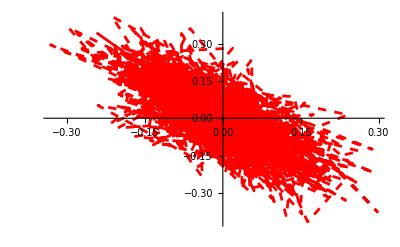

```mathematica
mfsPlot[{{mypoints[[All,1]],mypoints[[All,2]]}},PlotJoined->False]
```

#### Plot Commands

```mathematica
MLCPlot[data_,opts___]:=ListPlot
```

```mathematica
MLCPlotPeriodicOptics[lattice_,opts___]:=Block[{nslices,elemlist},nslices=Slices/.{opts}/.{Slices->1};elemlist=MADSplitElements[lattice,nslices];MLCGeneratePeriodicTwissTable[elemlist];Show[MADDraw[lattice,Labels->False,Lengths->False,WidthScale->Ceiling[0.2 Max[{MLCBETX,MLCBETY,10 MLCDX}]],Thick->0.002,Imagesize->600,Fontsize->10,Bends->False,Offset->5.5 Ceiling[0.2 Max[{MLCBETX,MLCBETY,10 MLCDX}]],DisplayFunction->Identity],mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY},{MLCS,10 MLCDX}},DisplayFunction->Identity,opts],Graphics[{Red,Text["\!\(\*SubscriptBox[\(β\), \(x\)]\)",{MLCS⟦First[Flatten[Position[MLCS,_?(#1>Last[MLCS] 0.1&)]]]⟧,MLCBETX⟦First[Flatten[Position[MLCS,_?(#1>Last[MLCS] 0.1&)]]]⟧+Max[MLCBETX] 0.1}],Blue,Text["\!\(\*SubscriptBox[\(β\), \(y\)]\)",{MLCS⟦First[Flatten[Position[MLCS,_?(#1>Last[MLCS] 0.2&)]]]⟧,MLCBETY⟦First[Flatten[Position[MLCS,_?(#1>Last[MLCS] 0.2&)]]]⟧+Max[MLCBETY] 0.1}],Black,Text["10 \!\(\*SubscriptBox[\(η\), \(x\)]\)",{MLCS⟦First[Flatten[Position[MLCS,_?(#1>Last[MLCS] 0.3&)]]]⟧,10 MLCDX⟦First[Flatten[Position[MLCS,_?(#1>Last[MLCS] 0.3&)]]]⟧+Max[MLCDX]}]}],ImageSize->{600,400},PlotRange->{{First[MLCS],Last[MLCS]},{5 Floor[0.2 Min[{MLCBETX,MLCBETY,10 MLCDX}]],6 Ceiling[0.2 Max[{MLCBETX,MLCBETY,10 MLCDX}]]}},Frame->True,DisplayFunction->$DisplayFunction,BaseStyle->{FontFamily->"Times",FontSize->18},FrameLabel->{"s [m]","Optical Functions [m]"}]]
```

#### Looking at Matrices

```mathematica
MLCMatrixInspect[M_]:=BarChart3D[M,ViewPoint->{-2.360,-2.220,0.975},XSpacing->1/2,YSpacing->1/2]
```

#### Synchrotron Radiation Integrals - only works for circular machines

```mathematica
integralSRI1[kx_,s_,h_,dx_,dpx_,β2_,ρ_]:=NIntegrate[(If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx]+dx (Cos[kx l]+h If[kx==0,l,Sin[kx l]/kx] Tan[β2]))/ρ,{l,0,s},Compiled->True]
```

```mathematica
MLCSRI1[latt_]:=Module[{kx,ky,ρ, h, n,L},
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
Plus@@((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];integralSRI1[kx,L,h,#⟦2,1⟧,#⟦2,2⟧,#⟦1,11⟧,ρ])&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="SectorBend"&],(Extract[mat,#]&/@pos)}])]
```

```mathematica
SR2Element[elem_]:=NIntegrate[(elem⟦6⟧/elem⟦3⟧)^2,{l,0,elem⟦3⟧}]
```

```mathematica
MLCSRI2[latt_]:=Plus@@(SR2Element[#]&/@(Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]))
```

```mathematica
SR3Element[elem_]:=NIntegrate[Abs[(elem⟦6⟧/elem⟦3⟧)^3],{l,0,elem⟦3⟧}]
```

```mathematica
MLCSRI3[latt_]:=Plus@@(SR3Element[#]&/@(Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]))
```

```mathematica
integralSRI4[kx_,s_,h_,dx_,dpx_,β2_,n_,ρ_]:=NIntegrate[(1-2n)(If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx]+dx (Cos[kx l]+h If[kx==0,l,Sin[kx l]/kx] Tan[β2]))/ρ^3,{l,0,s},Compiled->True]
```

```mathematica
MLCSRI4[latt_]:=Module[{kx,ky,ρ, h, n,L},
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
Plus@@((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];integralSRI4[kx,L,h,#⟦2,1⟧,#⟦2,2⟧,#⟦1,10⟧,n,ρ])&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="SectorBend"&],(Extract[mat,#]&/@pos)}])]
```

```mathematica
integralSRI5H[α_,β_,γ_,kx_,s_,h_,dx_,dpx_,ρ_]:=NIntegrate[((dx Cos[kx l]+If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx])^2+((β Cos[kx l]^2-2 α Cos[kx l] If[kx==0,l,Sin[kx l]/kx]+γ If[kx==0,l,Sin[kx l]/kx]^2) (dpx Cos[kx l]+If[kx==0,h l,(h Sin[kx l])/kx]-dx kx Sin[kx l])+(dx Cos[kx l]+If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx]) (-If[kx==0,l,Sin[kx l]/kx] (γ Cos[kx l]+kx α Sin[kx l])+Cos[kx l] (α Cos[kx l]+kx β Sin[kx l])))^2)/(β Cos[kx l]^2-2 α Cos[kx l] If[kx==0,l,Sin[kx l]/kx]+γ If[kx==0,l,Sin[kx l]/kx]^2)/Abs[ρ]^3,{l,0,s},Compiled->True]
```

```mathematica
MLCSRI5H[{elem_,input1_,input2_}]:=Module[{kx,ky,ρ, h, n,L},
Plus@@((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];If[kx=!=0,integralSRI5H[#⟦3,2⟧,#⟦3,1⟧,#⟦3,3⟧,kx,L,h,#⟦2,1⟧,#⟦2,2⟧,ρ],integralSRI5H2[#⟦3,2⟧,#⟦3,1⟧,#⟦3,3⟧,kx,L,h,#⟦2,1⟧,#⟦2,2⟧,ρ]])&/@{{elem,input1,input2}})]
```

```mathematica
MLCSRI5[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,ρ},
tmat=Transpose[MLCGeneratePeriodicTwissTable[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
Plus@@((MLCSRI5H[#])&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&],(Extract[mat,#]&/@pos),(Extract[tmat,#]&/@pos)}])]
```

```mathematica
MLCαc[latt_]:=MLCSRI1[latt]/MADLength[latt]
```

```mathematica
MLCϵ[latt_,energy_]:=1.4673594530853189*^-12 energy^2*If[ValueQ[MLCI5],MLCI5,MLCSRI5[latt]]/(If[ValueQ[MLCI2],MLCI2,MLCSRI2[latt]]-If[ValueQ[MLCI4],MLCI4,MLCSRI4[latt]])
```

```mathematica
MLCSRI[latt_]:={MLCI1=MLCSRI1[latt] Meter,MLCI2=MLCSRI2[latt]/Meter,MLCI3=MLCSRI3[latt]/Meter^2,MLCI4=MLCSRI4[latt]/Meter,MLCI5=MLCSRI5[latt]/Meter}
```

```mathematica
MLCϵ[latt_,energy_]:=Convert[(55 PlanckConstant (energy ElectronVolt Mega)^2)/(2 π (ElectronMass*SpeedOfLight^2)^2 32 √3 ElectronMass SpeedOfLight)*If[ValueQ[MLCI5],MLCI5,MLCSRI5[latt]]/((If[ValueQ[MLCI2],MLCI2,MLCSRI2[latt]])-(If[ValueQ[MLCI4],MLCI4,MLCSRI4[latt]])),Nano Meter]
```

```mathematica
MLCU0[latt_,energy_]:=Convert[(2 ClassicalElectronRadius(energy*Mega ElectronVolt)^4 (If[ValueQ[MLCI2],MLCI2,MLCSRI2[latt]]))/(3 (ElectronMass SpeedOfLight^2)^3),ElectronVolt Kilo]
```

```mathematica
MLCJx[latt_]:=1-(If[ValueQ[MLCI4],MLCI4,MLCSRI4[latt]])/(If[ValueQ[MLCI2],MLCI2,MLCSRI2[latt]])
```

```mathematica
MLCJϵ[latt_]:=2+(If[ValueQ[MLCI4],MLCI4,MLCSRI4[latt]])/(If[ValueQ[MLCI2],MLCI2,MLCSRI2[latt]])
```

```mathematica
MLCES[latt_,energy_]:=Convert[(55 PlanckConstant (energy ElectronVolt Mega)^2)/(2 π (ElectronMass*SpeedOfLight^2)^2 32 √3 ElectronMass SpeedOfLight)*If[ValueQ[MLCI3],MLCI3,MLCSRI3[latt]]/(2 (If[ValueQ[MLCI2],MLCI2,MLCSRI2[latt]])+(If[ValueQ[MLCI4],MLCI4,MLCSRI4[latt]])),Joules]
```

```mathematica
MLCτx[latt_,energy_]:=Convert[(3 ElectronMass^3 SpeedOfLight^5 MADLength[latt] Meter (Plus@@Select[MADFlatten[DIAMOND],#⟦2⟧==="SectorBend"&]⟦All,3⟧/(2 π)) Meter)/(2 π ClassicalElectronRadius MLCJx[latt] (energy Mega ElectronVolt)^3),Milli Second]
```

```mathematica
MLCτy[latt_,energy_]:=Convert[(3 ElectronMass^3 SpeedOfLight^5 MADLength[latt] Meter (Plus@@Select[MADFlatten[DIAMOND],#⟦2⟧==="SectorBend"&]⟦All,3⟧/(2 π)) Meter)/(2 π ClassicalElectronRadius 1 (energy Mega ElectronVolt)^3),Milli Second]
```

```mathematica
MLCτϵ[latt_,energy_]:=Convert[(3 ElectronMass^3 SpeedOfLight^5 MADLength[latt] Meter (Plus@@Select[MADFlatten[DIAMOND],#⟦2⟧==="SectorBend"&]⟦All,3⟧/(2 π)) Meter)/(2 π ClassicalElectronRadius MLCJϵ[latt] (energy Mega ElectronVolt)^3),Milli Second]
```

```mathematica
MLCϵx[latt_,energy_,κ_:0.01]:= MLCϵ[latt,energy]/(1+κ)
```

```mathematica
MLCϵy[latt_,energy_,κ_:0.01]:=(κ MLCϵ[latt,energy])/(1+κ)
```

#### BeamSizes

```mathematica
MLCσx[latt_,energy_]:=Block[{ϵx,es},ϵx=(MLCϵx[latt,energy] 10^-9/(Meter Nano));es=MLCES[latt,energy];(√(ϵx #⟦1⟧+es^2(#⟦2⟧)^2)&/@MapThread[List,{MLCGeneratePeriodicTwissTable[latt]⟦3⟧,MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]]⟦All,1⟧}])]
```

```mathematica
MLCσy[latt_,energy_]:=Block[{ϵy},ϵy=(MLCϵy[latt,energy] 10^-9/(Meter Nano));(√(ϵy #)&/@MLCGeneratePeriodicTwissTable[latt]⟦6⟧)]
```

```mathematica
MLCσprimex[latt_,energy_]:=Block[{ϵx,es},ϵx=(MLCϵx[latt,energy] 10^-9/(Meter Nano));es=MLCES[latt,energy];(√(ϵx #⟦1⟧+es^2(#⟦2⟧)^2)&/@MapThread[List,{MLCGeneratePeriodicTwissTable[latt]⟦5⟧,MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]]⟦All,2⟧}])]
```

```mathematica
MLCσprimey[latt_,energy_]:=Block[{ϵy},ϵy=(MLCϵy[latt,energy] 10^-9/(Meter Nano));(√(ϵy #)&/@MLCGeneratePeriodicTwissTable[latt]⟦8⟧)]
```

#### Chromaticity

```mathematica
QuadDisp[latt_]:=Block[{k,L,pos,mat,ρ,n,kx,ky,φ,h},
pos=(Position[MADFlatten[latt],"Quadrupole"]⟦All,1⟧-1)//.{0->-1};mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
If[#⟦1,4⟧<0,
(L=#⟦1,3⟧;k=Sqrt[-#⟦1,4⟧];QuadDispTableNeg[k,L,#⟦2,1⟧,#⟦2,2⟧]),(L=#⟦1,3⟧;k=Sqrt[#⟦1,4⟧];QuadDispTablePos[k,L,#⟦2,1⟧,#⟦2,2⟧])]&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="Quadrupole"&],(Extract[mat,#]&/@pos)}]]
```

```mathematica
QuadDispPrime[latt_]:=Block[{k,L,pos,mat,ρ,n,kx,ky,φ,h},
pos=(Position[MADFlatten[latt],"Quadrupole"]⟦All,1⟧-1)//.{0->-1};mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
If[#⟦1,4⟧<0,
(L=#⟦1,3⟧;k=Sqrt[-#⟦1,4⟧];QuadDispPrimeTableNeg[k,L,#⟦2,1⟧,#⟦2,2⟧]),(L=#⟦1,3⟧;k=Sqrt[#⟦1,4⟧];QuadDispPrimeTablePos[k,L,#⟦2,1⟧,#⟦2,2⟧])]&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="Quadrupole"&],(Extract[mat,#]&/@pos)}]]
```

```mathematica
QuadGamma[latt_]:=Block[{k,L,tmat,pos,mat,ρ,n,kx,ky,φ,h},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"Quadrupole"]⟦All,1⟧-1)//.{0->-1};
If[#⟦1,4⟧<0,
(L=#⟦1,3⟧;k=Sqrt[-#⟦1,4⟧];QuadGammaTableNeg[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L]),(L=#⟦1,3⟧;k=Sqrt[#⟦1,4⟧];QuadGammaTablePos[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L])]&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&],(Extract[tmat,#]&/@pos)}]]
```

```mathematica
QuadBeta[latt_]:=Block[{k,L,tmat,pos,mat,ρ,n,kx,ky,φ,h},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"Quadrupole"]⟦All,1⟧-1)//.{0->-1};
If[#⟦1,4⟧<0,
(L=#⟦1,3⟧;k=Sqrt[-#⟦1,4⟧];QuadBetaTableNeg[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L]),(L=#⟦1,3⟧;k=Sqrt[#⟦1,4⟧];QuadBetaTablePos[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L])]&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&],(Extract[tmat,#]&/@pos)}]]
```

```mathematica
DriftDisp[latt_]:=Block[{L,pos,mat,ρ,n,kx,ky,φ,h,k},
pos=(Position[MADFlatten[latt],"Drift"]⟦All,1⟧-1)//.{0->-1};
mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
(L=#⟦1,3⟧;DriftDispTable[L,#⟦2,1⟧,#⟦2,2⟧])&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="Drift"&],(Extract[mat,#]&/@pos)}]]
```

```mathematica
DriftDispPrime[latt_]:=Block[{L,pos,mat,ρ,n,kx,ky,φ,h,k},
pos=(Position[MADFlatten[latt],"Drift"]⟦All,1⟧-1)//.{0->-1};
mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
(L=#⟦1,3⟧;DriftDispPrimeTable[L,#⟦2,1⟧,#⟦2,2⟧])&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="Drift"&],(Extract[mat,#]&/@pos)}]]
```

```mathematica
DriftBeta[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"Drift"]⟦All,1⟧-1)//.{0->-1};
((L=#⟦1,3⟧;DriftBetaTable[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,L])&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Drift"&],(Extract[tmat,#]&/@pos)}])]
```

```mathematica
DriftGamma[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,ρ,L,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"Drift"]⟦All,1⟧-1)//.{0->-1};
((L=#⟦1,3⟧;DriftGammaTable[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,L])&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Drift"&],(Extract[tmat,#]&/@pos)}])]
```

```mathematica
DipoleDisp[latt_]:=Module[{kx,ky,ρ, h, n,L,φ,k},
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];DipoleDispTable[kx,L,h,#⟦2,1⟧,#⟦2,2⟧,#⟦1,11⟧,ρ])&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="SectorBend"&],(Extract[mat,#]&/@pos)}])]
```

```mathematica
DipoleDispPrime[latt_]:=Module[{kx,ky,ρ, h, n,L,φ,k},
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];DipoleDispPrimeTable[kx,L,h,#⟦2,1⟧,#⟦2,2⟧,#⟦1,10⟧,#⟦1,11⟧,ρ])&/@MapThread[List,{Select[MLCElementList[latt],#⟦2⟧==="SectorBend"&],(Extract[mat,#]&/@pos)}])]
```

```mathematica
DipoleBeta[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,L,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];DipoleBetaTable[#⟦3,2⟧,#⟦3,1⟧,#⟦3,3⟧,kx,#⟦1,11⟧,L])&/@MapThread[List,{MLCElementList[Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]],(Extract[mat,#]&/@pos),(Extract[tmat,#]&/@pos)}])]
```

```mathematica
DipoleGamma[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,L,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{3,4,5}⟧];
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];DipoleGammaTable[#⟦3,2⟧,#⟦3,1⟧,#⟦3,3⟧,kx,#⟦1,10⟧,#⟦1,11⟧,L])&/@MapThread[List,{MLCElementList[Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]],(Extract[mat,#]&/@pos),(Extract[tmat,#]&/@pos)}])]
```

```mathematica
QuadBetaY[latt_]:=Block[{k,L,tmat,pos,mat,ρ,n,kx,ky,φ,h},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{6,7,8}⟧];
pos=(Position[MADFlatten[latt],"Quadrupole"]⟦All,1⟧-1)//.{0->-1};
If[#⟦1,4⟧<0,
(L=#⟦1,3⟧;k=Sqrt[-#⟦1,4⟧];QuadBetaYTableNeg[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L]),(L=#⟦1,3⟧;k=Sqrt[#⟦1,4⟧];QuadBetaYTablePos[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L])]&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&],(Extract[tmat,#]&/@pos)}]]
```

```mathematica
DriftBetaY[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,L,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{6,7,8}⟧];
pos=(Position[MADFlatten[latt],"Drift"]⟦All,1⟧-1)//.{0->-1};
((L=#⟦1,3⟧;DriftBetaYTable[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,L])&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Drift"&],(Extract[tmat,#]&/@pos)}])]
```

```mathematica
DipoleBetaY[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,L,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{6,7,8}⟧];
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];φ=k h 0(1+Sin[β]^2)/Cos[β];DipoleBetaYTable[#⟦3,2⟧,#⟦3,1⟧,#⟦3,3⟧,ky,#⟦1,11⟧,#⟦1,11⟧,φ,h,L])&/@MapThread[List,{MLCElementList[Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]],(Extract[mat,#]&/@pos),(Extract[tmat,#]&/@pos)}])]
```

```mathematica
DipoleGammaY[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,L,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{6,7,8}⟧];
pos=(Position[MADFlatten[latt],"SectorBend"]⟦All,1⟧-1);mat=(#*{1,1,0,0,0,1})&/@MLCPropagateDispersion[MLCFindPeriodicDispersion[MLCOneTurnRMatrix[MLCRMatrices[latt]]],MLCRMatrices[latt]];
((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];φ=k h 0(1+Sin[β]^2)/Cos[β];DipoleGammaYTable[#⟦3,2⟧,#⟦3,1⟧,#⟦3,3⟧,ky,#⟦1,11⟧,#⟦1,11⟧,h,L])&/@MapThread[List,{MLCElementList[Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]],(Extract[mat,#]&/@pos),(Extract[tmat,#]&/@pos)}])]
```

```mathematica
QuadGammaY[latt_]:=Block[{k,L,tmat,pos,mat,ρ,n,kx,ky,φ,h},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{6,7,8}⟧];
pos=(Position[MADFlatten[latt],"Quadrupole"]⟦All,1⟧-1)//.{0->-1};
If[#⟦1,4⟧<0,
(L=#⟦1,3⟧;k=Sqrt[-#⟦1,4⟧];QuadGammaYTableNeg[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L]),(L=#⟦1,3⟧;k=Sqrt[#⟦1,4⟧];QuadGammaYTablePos[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,k,L])]&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&],(Extract[tmat,#]&/@pos)}]]
```

```mathematica
DriftGammaY[latt_]:=Block[{H,β,βprime,η,ηprime,pos,mat,tpos,tmat,L,ρ,n,kx,ky,φ,h,k},
tmat=Transpose[MLCGeneratePeriodicTwissTableNoOut[MADFlatten[latt]]⟦{6,7,8}⟧];
pos=(Position[MADFlatten[latt],"Drift"]⟦All,1⟧-1)//.{0->-1};
((L=#⟦1,3⟧;DriftGammaYTable[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,L])&/@MapThread[List,{Select[MADFlatten[latt],#⟦2⟧==="Drift"&],(Extract[tmat,#]&/@pos)}])]
```

```mathematica
QuadDispTableNeg[k_,s_,dx_,dpx_]:=NIntegrate[dx Cosh[k L]+(dpx Sinh[k L])/k ,{L,0,s}]
```

```mathematica
QuadDispPrimeTableNeg[k_,s_,dx_,dpx_]:=NIntegrate[dpx Cosh[k L]+dx k Sinh[k L] ,{L,0,s}]
```

```mathematica
QuadDispTablePos[k_,s_,dx_,dpx_]:=NIntegrate[dx Cos[k L]+(dpx Sin[k L])/k ,{L,0,s}]
```

```mathematica
QuadDispPrimeTablePos[k_,s_,dx_,dpx_]:=NIntegrate[dpx Cos[k L]-dx k Sin[k L] ,{L,0,s}]
```

```mathematica
QuadBetaTablePos[α_,β_,γ_,k_,s_]:=NIntegrate[Cos[k L] (β Cos[k L]-(α Sin[k L])/k)+(Sin[k L] (-α Cos[k L]+(γ Sin[k L])/k))/k,{L,0,s}]
```

```mathematica
QuadBetaTableNeg[α_,β_,γ_,k_,s_]:=NIntegrate[Cosh[k L] (β Cosh[k L]-(α Sinh[k L])/k)+(Sinh[k L] (-α Cosh[k L]+(γ Sinh[k L])/k))/k,{L,0,s}]
```

```mathematica
QuadGammaTablePos[α_,β_,γ_,k_,s_]:=NIntegrate[Cos[k L] (γ Cos[k L]+k α Sin[k L])-k Sin[k L] (-α Cos[k L]-k β Sin[k L]),{L,0,s}]
```

```mathematica
QuadGammaTableNeg[α_,β_,γ_,k_,s_]:=NIntegrate[Cosh[k L] (γ Cosh[k L]-k α Sinh[k L])+k Sinh[k L] (-α Cosh[k L]+k β Sinh[k L]),{L,0,s}]
```

```mathematica
DriftDispTable[s_,dx_,dpx_]:=NIntegrate[dx+dpx L ,{L,0,s}]
```

```mathematica
DriftDispPrimeTable[s_,dx_,dpx_]:=NIntegrate[dpx ,{L,0,s}]
```

```mathematica
DriftBetaTable[α_,β_,γ_,s_]:=NIntegrate[-L α+β+L (-α+L γ),{L,0,s}]
```

```mathematica
DriftGammaTable[α_,β_,γ_,s_]:=NIntegrate[γ,{L,0,s}]
```

```mathematica
DipoleDispTable[kx_,s_,h_,dx_,dpx_,β2_,ρ_]:=NIntegrate[(If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx]+dx (Cos[kx l]+h If[kx==0,l,Sin[kx l]/kx] Tan[β2])),{l,0,s}]
```

```mathematica
DipoleDispPrimeTable[kx_,s_,h_,dx_,dpx_,β1_,β2_,ρ_]:=NIntegrate[If[kx==0,h l,(h Sin[kx l])/kx]+h If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2] Tan[β1]+dpx (Cos[kx l]+h If[kx==0,l,Sin[kx l]/kx] Tan[β1])+dx (-kx Sin[kx l]+h Cos[kx l] Tan[β1]+h (Cos[kx l]+h If[kx==0,l,Sin[kx l]/kx] Tan[β1]) Tan[β2]),{l,0,s}]
```

```mathematica
DipoleBetaTable[α_,β_,γ_,kx_,s_]:=NIntegrate[(β Cos[kx l]^2-2 α Cos[kx l] If[kx==0,l,Sin[kx l]/kx]+γ If[kx==0,l,Sin[kx l]/kx]^2),{l,0,s}]
```

```mathematica
DipoleBetaTable[α_,β_,γ_,kx_,β2_,s_]:=NIntegrate[β Cos[kx L]^2-2 Cos[kx L] If[kx==0,L,Sin[kx L]/kx] (α-h β Tan[β2])+If[kx==0,L,Sin[kx L]/kx]^2 (γ+h Tan[β2] (-2 α+h β Tan[β2])),{L,0,s}]
```

```mathematica
DipoleGammaTable[α_,β_,γ_,k_,β1_,β2_,s_]:=NIntegrate[h^2 If[kx==0,L,Sin[kx L]/kx]^2 Tan[β1]^2 (γ+h Tan[β2] (-2 α+h β Tan[β2]))+kx (kx β Sin[kx L]^2+Sin[2 kx L] (α-h β (Tan[β1]+Tan[β2])))+Cos[kx L]^2 (γ+h (Tan[β1]+Tan[β2]) (-2 α+h β (Tan[β1]+Tan[β2])))+2 h If[kx==0,L,Sin[kx L]/kx] Tan[β1] (kx Sin[kx L] (α-h β Tan[β2])+Cos[kx L] (γ+h Tan[β2] (-2 α+h β Tan[β2])+h Tan[β1] (-α+h β Tan[β2]))),{L,0,s}]
```

```mathematica
QuadBetaYTablePos[α_,β_,γ_,k_,s_]:=NIntegrate[β Cosh[k L]^2+(γ Sinh[k L]^2-k α Sinh[2 k L])/k^2,{L,0,s}]
```

```mathematica
QuadBetaYTableNeg[α_,β_,γ_,k_,s_]:=NIntegrate[β Cos[k L]^2+(γ Sin[k L]^2-k α Sin[2 k L])/k^2,{L,0,s}]
```

```mathematica
DriftBetaYTable[α_,β_,γ_,s_]:=NIntegrate[-2 L α+β+L^2 γ,{L,0,s,s/10}]
```

```mathematica
DipoleBetaYTable[α_,β_,γ_,ky_,β1_,β2_,φ_,h_,s_]:=NIntegrate[β Cos[ky L]^2-2 Cos[ky L] If[ky==0,L,Sin[ky L]/ky] (α+h β Tan[β2-φ])+If[ky==0,L,Sin[ky L]/ky]^2 (γ+h Tan[β2-φ] (2 α+h β Tan[β2-φ])),{L,0,s}]
```

```mathematica
QuadGammaYTablePos[α_,β_,γ_,k_,s_]:=NIntegrate[γ Cosh[k L]^2+k (k β Sinh[k L]^2-α Sinh[2 k L]),{L,0,s}]
```

```mathematica
QuadGammaYTableNeg[α_,β_,γ_,k_,s_]:=NIntegrate[Cos[k L] (γ Cos[k L]+k α Sin[k L])-k Sin[k L] (-α Cos[k L]-k β Sin[k L]),{L,0,s}]
```

```mathematica
DriftGammaYTable[α_,β_,γ_,s_]:=NIntegrate[γ,{L,0,s,s/10}]
```

```mathematica
DipoleGammaYTable[α_,β_,γ_,ky_,β1_,β2_,h_,s_]:=NIntegrate[h^2 If[ky==0,L,Sin[ky L]/ky]^2 Tan[β1]^2 (γ+h Tan[β2] (2 α+h β Tan[β2]))+ky (ky β Sin[ky L]^2+Sin[2 ky L] (α+h β (Tan[β1]+Tan[β2])))+Cos[ky L]^2 (γ+h (Tan[β1]+Tan[β2]) (2 α+h β (Tan[β1]+Tan[β2])))-2 h If[ky==0,L,Sin[ky L]/ky] Tan[β1] (ky Sin[ky L] (α+h β Tan[β2])+Cos[ky L] (γ+h Tan[β1] (α+h β Tan[β2])+h Tan[β2] (2 α+h β Tan[β2]))),{L,0,s}]
```

```mathematica
QuadK2[latt_]:=Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&]⟦All,4⟧
```

```mathematica
QuadChromX[latt_]:=Block[{βx,γ,h,K2,ηx,ηxprime,L},βx=QuadBeta[latt];γ=QuadGamma[latt];h=Table[0,{Length[Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&]]}];hprime=h;γ=QuadGamma[latt];K2=QuadK2[latt];ηx=QuadDisp[latt];ηxprime=QuadDispPrime[latt];L=Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&]⟦All,3⟧;
-(1/(4 π)(#⟦1⟧(#⟦7⟧-2 (#⟦5⟧)^2-2 #⟦7⟧ #⟦5⟧ #⟦2⟧-#⟦6⟧ #⟦3⟧)+#⟦1⟧ #⟦5⟧ #⟦2⟧((#⟦5⟧)^2-#⟦7⟧)+#⟦4⟧ #⟦5⟧ #⟦2⟧))&/@Transpose[{βx,ηx,ηxprime,γ,h,hprime,K2}]
]
```

```mathematica
BendChromX[latt_]:=Block[{βx,γ,h,K2,ηx,ηxprime,L},βx=DipoleBeta[latt];γ=DipoleGamma[latt];h=Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]⟦All,6⟧;hprime=h;K2=Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]⟦All,4⟧;ηx=DipoleDisp[latt];ηxprime=DipoleDispPrime[latt];L=Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]⟦All,3⟧;
-(1/(4 π)(#⟦1⟧(#⟦7⟧-2 (#⟦5⟧)^2-2 #⟦7⟧ #⟦5⟧ #⟦2⟧-#⟦6⟧ #⟦3⟧)+#⟦1⟧ #⟦5⟧ #⟦2⟧((#⟦5⟧)^2-#⟦7⟧)+#⟦4⟧ #⟦5⟧ #⟦2⟧))&/@Transpose[{βx,ηx,ηxprime,γ,h,hprime,K2}]
]
```

```mathematica
TotalChromX[latt_]:=Plus@@Flatten[{QuadChromX[latt],BendChromX[latt]}]
```

```mathematica
QuadChromY[latt_]:=Block[{βy,γ,h,K2,ηx,ηxprime,L},βy=QuadBetaY[latt];γ=QuadGammaY[latt];h=Table[0,{Length[Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&]]}];hprime=h;K2=QuadK2[latt];ηx=QuadDisp[latt];ηxprime=QuadDispPrime[latt];L=Select[MADFlatten[latt],#⟦2⟧==="Quadrupole"&]⟦All,3⟧;
-(1/(4 π)(#⟦1⟧(-#⟦7⟧+#⟦7⟧ #⟦5⟧ #⟦2⟧+#⟦6⟧ #⟦3⟧)))&/@Transpose[{βy,ηx,ηxprime,γ,h,hprime,K2}]
]
```

```mathematica
BendChromY[latt_]:=Block[{βy,γ,h,K2,ηx,ηxprime,L},βy=DipoleBetaY[latt];γ=DipoleGammaY[latt];h=Table[0,{Length[Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]]}];hprime=h;K2=Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]⟦All,4⟧;ηx=DipoleDisp[latt];ηxprime=DipoleDispPrime[latt];L=Select[MADFlatten[latt],#⟦2⟧==="SectorBend"&]⟦All,3⟧;
-(1/(4 π)(#⟦1⟧(-#⟦7⟧+#⟦7⟧ #⟦5⟧ #⟦2⟧+#⟦6⟧ #⟦3⟧)))&/@Transpose[{βy,ηx,ηxprime,γ,h,hprime,K2}]
]
```

```mathematica
TotalChromY[latt_]:=Plus@@Flatten[{QuadChromY[latt],BendChromY[latt]}]
```

```mathematica
MLCChromaticity[latt_]:={TotalChromX[MADFlatten[latt]],TotalChromY[MADFlatten[latt]]}
```

#### EndPackage Functions

```mathematica
End[]
```

MLC`mlc`Private`

```mathematica
EndPackage[]
```

## Example Use - The SRS

```mathematica
Quit[]
```

```mathematica
$Path=Append[Drop[$Path,-1],"c:\\madinputv6"];
```

```mathematica
<<MLC`MLC`
```

Version 2.21 of Madtomma`Mfs`Mfs` loaded.  Note function name changes since Version 1.x:
interpretDescriptors→mfsInterpretKeys
keyValue→mfsKeyValue
columnNames→mfsColumnNames
descriptorNames→mfsKeyNames
colValue→mfsColumnValue
addDescriptor→mfsAddKey
editDescriptor→mfsEditKey
deleteDescriptor→mfsDeleteKey
symplecticJ→SymplecticJ

Global`Thin::shdw: Symbol "Thin" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

### Creating Element Definitions

#### Drifts

```mathematica
drift[D1,0.4725,"D1",XAp->0.035,YAp->0.01]
```

```mathematica
drift[D2,2.167,"D2",XAp->0.035,YAp->0.01]
```

```mathematica
drift[D3,0.3725,"D3",XAp->0.035,YAp->0.01]
```

#### Bends

```mathematica
sbend[BD,2.188001,0.0,(2 Pi/16)//N,"BD",E1->0.0,E2->0.0,XAp->0.035,YAp->0.01]
```

#### Quads

```mathematica
quad[Q1,0.3,-1.5633944,"Q1",XAp->0.035,YAp->0.01]
```

```mathematica
quad[Q2,0.5,1.2783629,"Q2",XAp->0.035,YAp->0.01]
```

### Creating Lines

```mathematica
SRS={D1,Q1,D2,Q2,D3,BD}
```

{{{D1,Drift,0.4725,---,---,---,D1}},{{Q1,Quadrupole,0.3,-1.56339,---,---,Q1}},{{D2,Drift,2.167,---,---,---,D2}},{{Q2,Quadrupole,0.5,1.27836,---,---,Q2}},{{D3,Drift,0.3725,---,---,---,D3}},{{BD,SectorBend,2.188,0.,---,0.392699,BD}}}

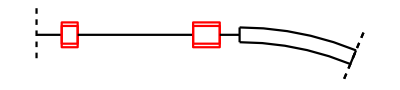

```mathematica
MADDraw[SRS]
```

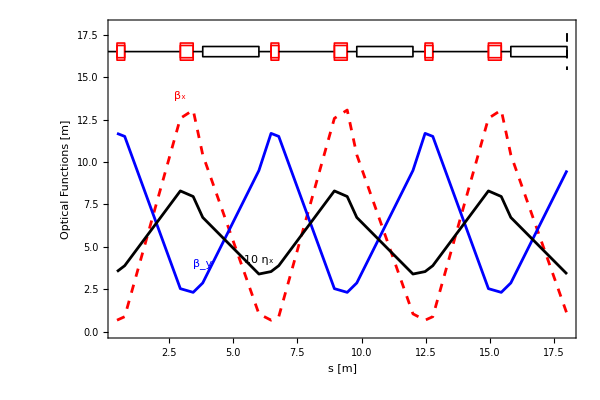

```mathematica
MLCPlotPeriodicOptics[Table[SRS,{3}],Slices->25,Dashing->True,Joined->True,PlotRange->All]
```

```mathematica
MLCPlotOptics[{SRS},Slices->50,PlotJoined->False]
```

MLCPlotOptics[{{{{D1,Drift,0.4725,---,---,---,D1}},{{Q1,Quadrupole,0.3,-1.56339,---,---,Q1}},{{D2,Drift,2.167,---,---,---,D2}},{{Q2,Quadrupole,0.5,1.27836,---,---,Q2}},{{D3,Drift,0.3725,---,---,---,D3}},{{BD,SectorBend,2.188,0.,---,0.392699,BD}}}},Slices→50,PlotJoined→False]

```mathematica
MLCTwissFunctions[SRS,100];//Timing
```

{0.,Null}

```mathematica
MLCGeneratePeriodicTwissTable[MADSplitElements[SRS,100]];//Timing
```

{0.453,Null}

```mathematica
MADInfo[SRS]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | D1 | Drift | 0.4725 | --- | --- | --- | D1 | 0.4725
2 | Q1 | Quadrupole | 0.3 | -1.56339 | --- | --- | Q1 | 0.7725
3 | D2 | Drift | 2.167 | --- | --- | --- | D2 | 2.9395
4 | Q2 | Quadrupole | 0.5 | 1.27836 | --- | --- | Q2 | 3.4395
5 | D3 | Drift | 0.3725 | --- | --- | --- | D3 | 3.812
6 | BD | SectorBend | 2.188 | 0. | --- | 0.392699 | BD | 6.

Total Length = 6. m

```mathematica
SRSC=Table[SRS,{16}];
```

```mathematica
MADFlatten[{SRSC}]//Length
```

96

```mathematica
MLCFindPeriodicTwiss[MLCOneTurnRMatrix[MLCRMatrices[{SRS}]]]
```

{{1.06081,0.737318,1.45515},{9.50129,-2.17051,0.601088}}

```mathematica
MLCOneTurnRMatrix[MLCRMatrices[{SRS}]]//MatrixForm
```

(-0.305668 | 0.672692 | 0. | 0. | 0. | 0.42412
-0.922759 | -1.24078 | 0. | 0. | 0. | 0.382683
0. | 0. | -1.78667 | 9.092 | 0. | 0.
0. | 0. | -0.575196 | 2.36735 | 0. | 0.
-0.274387 | -0.783669 | 0. | 0. | 1. | -0.0558042
0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
MLCFindPeriodicPhase[MLCOneTurnRMatrix[MLCRMatrices[{SRS}]]]
```

{2.45471,1.27621}

```mathematica
MLCGenerateTwissTable[{MADFlatten[MADSplitElements[SRS,10]]},MLCFindPeriodicTwiss[#],{0,0},MLCFindPeriodicDispersion[#]]&[MLCOneTurnRMatrix[MLCRMatrices[{SRS}]]];
```

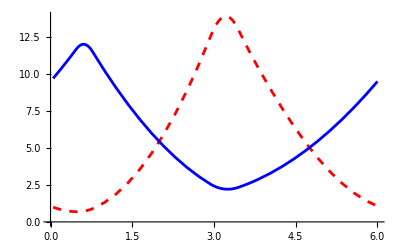

```mathematica
mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY}}]
```

```mathematica
Last[MLCMUX/(2 Pi)-MLCMUX]
```

-2.06403

```mathematica
MLCSRI[SRS]*16
```

{2.77089 Meter,1.1277/Meter,0.202397/Meter^2,0.0892574/Meter,0.0190605/Meter}

```mathematica
MLCϵ[SRSC,2000]
```

107.744 Meter Nano

```mathematica
MLCϵx[SRSC,2000,0.01]
```

106.677 Meter Nano

```mathematica
MLCαc[SRSC]
```

0.0288635

```mathematica
MLCU0[SRSC,2000]
```

15.8772 ElectronVolt Kilo

```mathematica
MLCES[SRSC,2000]
```

5.06717×10^-7

```mathematica
MLCJx[SRSC]
```

0.92085

```mathematica
MLCJϵ[SRSC]
```

2.07915

```mathematica
{ξx,ξy}=MLCChromaticity[SRSC]
```

{-10.3795,-5.22393}

```mathematica
MLCLinearDriftMatrix[D1⟦1⟧].{1,1,0,0,0,1}
```

{1.4725,1.,0.,0.,0.,1.}

### Perform Basic Optics Plots

#### Beta Functions and Dispersion

```mathematica
plot1=MADDraw[SRS,Labels->False,Lengths->False,WidthScale->5,Thick->0.002,Imagesize->600,Fontsize->10,Bends->False,Offset->30,DisplayFunction->Identity];
```

```mathematica
plot2=mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY},{MLCS,10 MLCDY}},DisplayFunction->Identity];
```

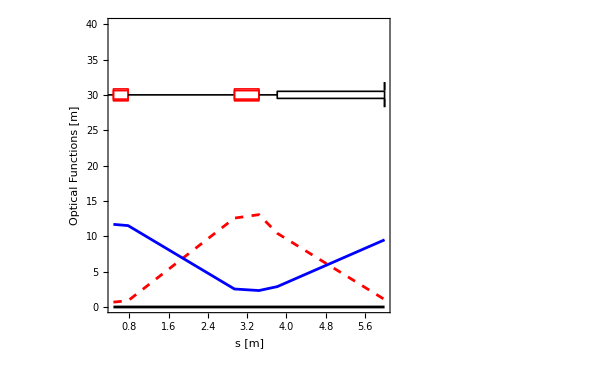

```mathematica
Show[plot2,plot1,Graphics[{Text["Bx",{21,24}],Text["By",{19,36}],Text["10*Dx",{8,2}]}],ImageSize->{600,400},PlotRange->{{First[MLCS],Last[MLCS]},{0,40}},Frame->True,DisplayFunction->$DisplayFunction,BaseStyle->{FontFamily->"Times",FontSize->18},FrameLabel->{"s [m]","Optical Functions [m]"}]
```

#### Phase Advance and Tunes

```mathematica
plot3=MADDraw[SRS,Labels->False,Lengths->False,WidthScale->2,Thick->0.002,Imagesize->600,Fontsize->10,Bends->False,Offset->6];
```

```mathematica
plot4=mfsPlot[{{MLCS,MLCMUX},{MLCS,MLCMUY}},DisplayFunction->Identity];
```

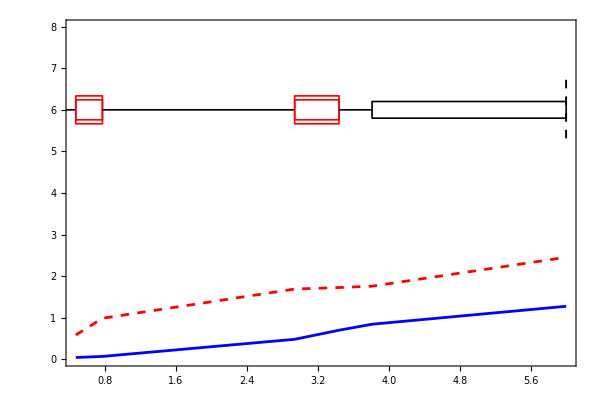

```mathematica
Show[plot3,plot4,ImageSize->{600,400},PlotRange->{{First[MLCS],Last[MLCS]},{0,8}},Frame->True,DisplayFunction->$DisplayFunction]
```

```mathematica
axistunex=Last[MLCMUX]
```

2.45471

```mathematica
axistuney=Last[MLCMUY]
```

1.27621

```mathematica
{6 axistunex,6 axistuney}
```

{14.7282,7.65729}

```mathematica
{Mean[MLCBETX],Mean[MLCBETY]}
```

{6.45033,6.7415}

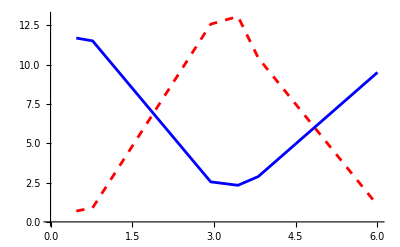

```mathematica
mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY}}]
```

## Testing Non-Paraxial Transport

### Creating Element Definitions

#### Drifts

```mathematica
drift[D1,1,"D1",XAp->0.035,YAp->0.01]
```

```mathematica
drift[D2,1,"D2",XAp->0.035,YAp->0.01]
```

#### Quads

```mathematica
quad[Q1,20,0.22,"Q1",XAp->0.035,YAp->0.01]
```

```mathematica
quad[Q2,0.5,-1,"Q2",XAp->0.035,YAp->0.01]
```

### Creating Lines

```mathematica
testline:={D1,D1,D1,D1,D1}
```

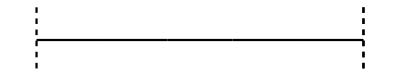

```mathematica
MADDraw[testline]
```

```mathematica
MLCGetElementLengths[testline]
```

{1,1,1,1,1}

```mathematica
MLCPropagateNonParaxialRay[{0,0.01,0,0,0.1,0},MLCRMatrices[testline],MLCGetElementLengths[testline]]
```

{{0.01,0.01,0.,0.,0.09995,0.},{0.02,0.01,0.,0.,0.0999,0.},{0.03,0.01,0.,0.,0.09985,0.},{0.04,0.01,0.,0.,0.0998,0.},{0.05,0.01,0.,0.,0.09975,0.}}

#### Create Initial Distributions

Define desired bunch length (in picoseconds) - this is the RMS value - i.e. the Standard Deviation calculated from a set of samples will be this value.

```mathematica
bunchlength:=0.2;
```

Define energy spread (relative energy spread) - again, this is the rms value as above.

```mathematica
percent:=10^-2;
```

```mathematica
energyspread:=0.0 percent
```

Define energy chirp per/mm

```mathematica
energychirp:=0.0 percent/mm
```

```mathematica
numberofparticles:=10^3
```

```mathematica
normalisedemittance:=5 mm mrad
```

```mathematica
erlenergy:=2
```

```mathematica
erlgamma:=erlenergy/Convert[N[ElectronMass c^2/MeV],1]
```

```mathematica
emittance:=normalisedemittance /erlgamma
```

```mathematica
{{betxinitial,alfxinitial,gamxinitial},{betyinitial,alfyinitial,gamyinitial}}={MLCBetaGamma[10,0],MLCBetaGamma[10,0]}
```

{{10,0,1/10},{10,0,1/10}}

```mathematica
sigmaxinitial=√(emittance betxinitial);sigmayinitial=√(emittance betyinitial);sigmaxpinitial=√(emittance gamxinitial);sigmaypinitial=√(emittance gamxinitial);
```

Gaussian input distribution of particles:

```mathematica
glongdistribution=Subscript[c, SI] GaussianEnsemble[numberofparticles,0,bunchlength 10^-12,6];
```

```mathematica
ginputdistribution=Transpose[{GaussianEnsemble[numberofparticles,0,sigmaxinitial,6],GaussianEnsemble[numberofparticles,0,sigmaxpinitial,6],GaussianEnsemble[numberofparticles,0,sigmayinitial,6],GaussianEnsemble[numberofparticles,0,sigmaypinitial,6],glongdistribution,GaussianEnsemble[numberofparticles,0,energyspread,6]+energychirp glongdistribution}];
```

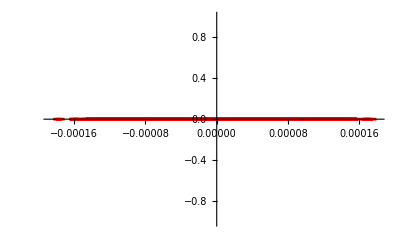

```mathematica
mfsPlot[{{ginputdistribution[[All,5]],ginputdistribution[[All,6]]}},PlotJoined->False]
```

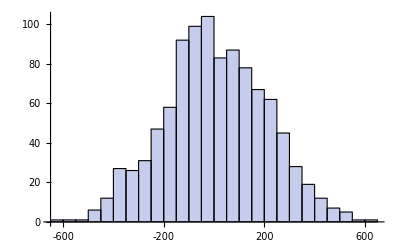

```mathematica
Histogram[10^15/Subscript[c, SI] ginputdistribution[[All,5]]]
```

#### Perform Tracking and Plot Results

```mathematica
trackinglattice=MADSplitElements[testline,5];
```

```mathematica
trackingdata=MLCPropagateNonParaxialRay[#,MLCRMatrices[trackinglattice],MLCGetElementLengths[trackinglattice]]&/@ginputdistribution;
```

```mathematica
trackingdataparaxial=MLCPropagateRay[#,MLCRMatrices[trackinglattice]]&/@ginputdistribution;
```

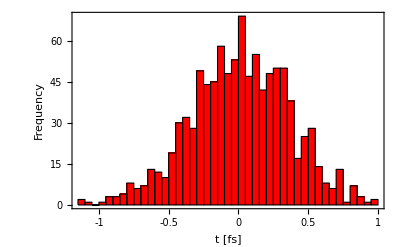

```mathematica
Histogram[1000 trackingdata⟦All,1,2⟧,BarStyle->Red,Frame->True,GridLines->None,BaseStyle->{FontFamily->"Courier",FontSize->14},FrameLabel->{"t [fs]","Frequency","Divergence: "<>ToString[10^3 StandardDeviation[trackingdata⟦All,1,2⟧]]<>" mrad",""}]
```

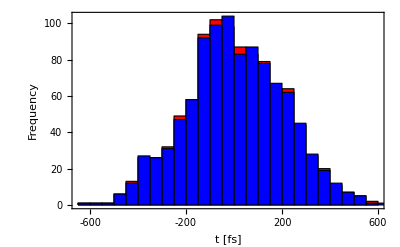

```mathematica
Show[Histogram[(10^15 trackingdata⟦All,-1,5⟧)/Subscript[c, SI],BarStyle->Red,DisplayFunction->Identity],Histogram[(10^15 trackingdataparaxial⟦All,-1,5⟧)/Subscript[c, SI],BarStyle->Blue,DisplayFunction->Identity],Frame->True,GridLines->None,BaseStyle->{FontFamily->"Courier",FontSize->14},FrameLabel->{"t [fs]","Frequency","Bunch Length: "<>ToString[(10^15 StandardDeviation[trackingdata⟦All,-1,5⟧])/Subscript[c, SI]]<>"/"<>ToString[(10^15 StandardDeviation[trackingdataparaxial⟦All,-1,5⟧])/Subscript[c, SI]]<>" fs",""},DisplayFunction->$DisplayFunction,ImageSize->{400,Automatic}]
```

```mathematica
,AspectRatio->0.4,Frame->True,GridLines->None,BaseStyle->{FontFamily->"Courier",FontSize->14},FrameLabel->{"t [fs]","Frequency","Bunch Length: "<>ToString[(10^15 StandardDeviation[trackingdata⟦All,n,5⟧])/Subscript[c, SI]]<>" fs",""},DisplayFunction->$DisplayFunction
```

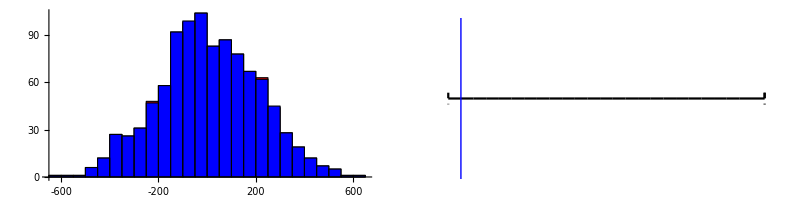
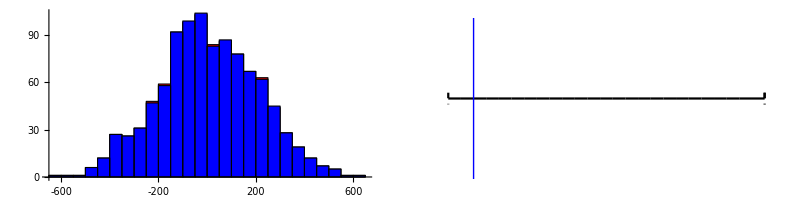
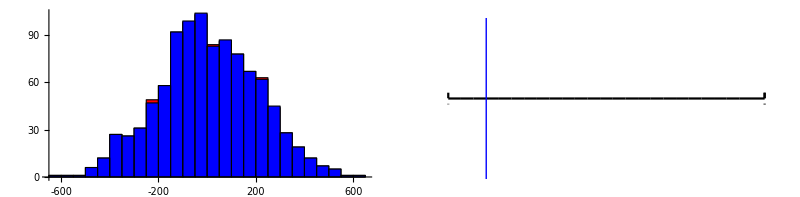
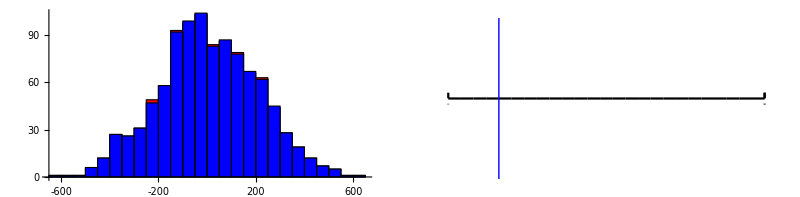
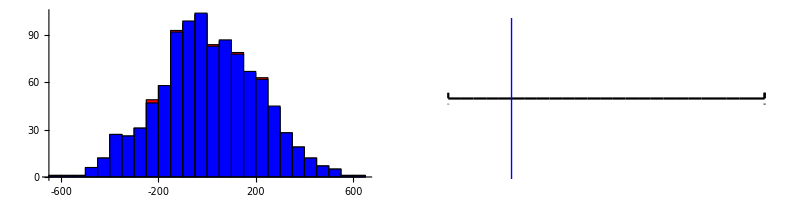
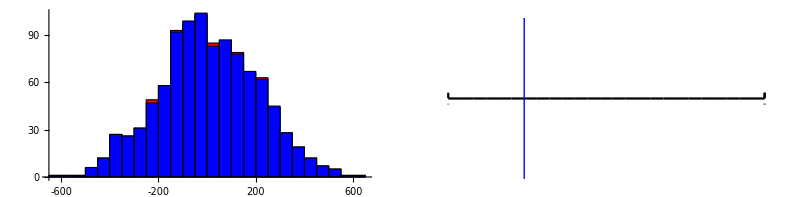
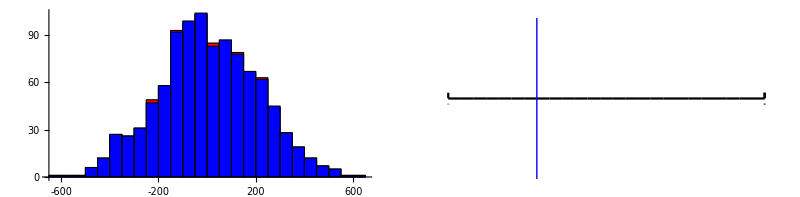
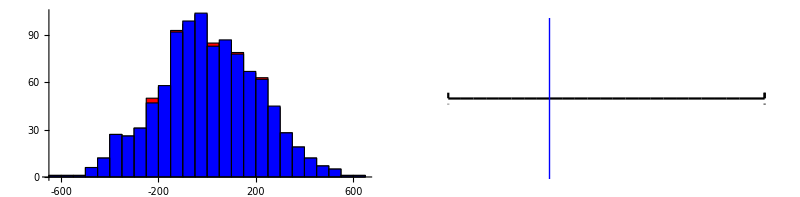

```mathematica
Table[GraphicsRow[{Show[Histogram[(10^15 trackingdata⟦All,n,5⟧)/Subscript[c, SI],BarStyle->Red,DisplayFunction->Identity],Histogram[(10^15 trackingdataparaxial⟦All,n,5⟧)/Subscript[c, SI],BarStyle->Blue,DisplayFunction->Identity]],Show[MADDraw[trackinglattice,Bends->False,WidthScale->0.2,DisplayFunction->Identity],Graphics[{Blue,Line[{{#1,-1},{#1,1}}]}]&[MADGetLengths[trackinglattice]⟦n⟧]]}],{n,1,Length[MADGetLengths[trackinglattice]]}]
```

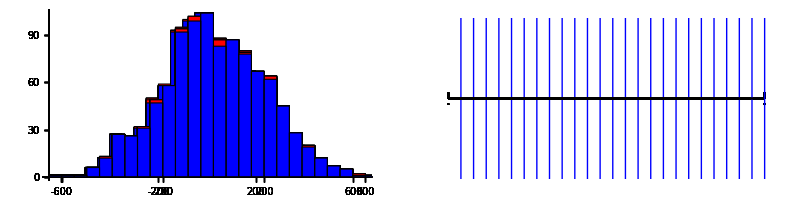

```mathematica
Show[%]
```

## Testing Phase Advance Calculations

#### Additional MAD Functions

```mathematica
MADWriteInitialConditions[ref_,lname_,lbetx_,lalfx_,lbety_,lalfy_,ldx_,ldpx_,ldy_,ldpy_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
lname<>": beta0, &\n
betx="<>ToString[lbetx]<>",alfx="<>ToString[lalfx]<>",&;\n
bety="<>ToString[lbety]<>",alfy="<>ToString[lalfy]<>",&;\n
dx="<>ToString[ldx]<>",dpx="<>ToString[ldpx]<>",&;\n
dy="<>ToString[ldy]<>",dpy="<>ToString[ldpy]<>";\n"];
Close[datafile];]
```

```mathematica
MADCreateTwissData[ref_,deltap_,startlabel_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
"print,full;\n
select,flag=optics,full;\n
optics,Beta0="<>startlabel<>",filename=\"twissoptics.txt\",deltap="<>ToString[deltap]<>",&\n
columns=name,s,l,betx,alfx,bety,alfy,mux,muy;\n"];
Close[datafile];]
```

```mathematica
MADCreateDispersionData[ref_,deltap_,startlabel_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
"print,full;\n
select,flag=optics,full;\n
optics,Beta0="<>startlabel<>",filename=\"dispersionoptics.txt\",deltap="<>ToString[deltap]<>",&\n
columns=name,s,dx,dpx,dy,dpy;\n"];
Close[datafile];]
```

```mathematica
MADCreateOrbitData[ref_,deltap_,startlabel_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
"print,full;\n
select,flag=optics,full;\n
optics,Beta0="<>startlabel<>",filename=\"orbitoptics.txt\",deltap="<>ToString[deltap]<>",&\n
columns=name,s,x,y;\n"];
Close[datafile];]
```

```mathematica
MADCallFile[ref_,filename_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
"call,"<>ToString[filename]<>"\n"];
Close[datafile];]
```

```mathematica
MADMyTwiss[ref_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
"print,#s/#e;\n
twiss,save;\n"];
Close[datafile];]
```

```mathematica
MADCreateOpticsData[ref_,deltap_,startlabel_]:=(MADCreateTwissData[ref,deltap,startlabel];MADCreateDispersionData[ref,deltap,startlabel];MADCreateOrbitData[ref,deltap,startlabel];)
```

```mathematica
MADReadOpticsData[]:=(mfsInterpret[tfsRead["twissoptics.txt"]];mfsInterpret[tfsRead["dispersionoptics.txt"]];mfsInterpret[tfsRead["orbitoptics.txt"]];)
```

```mathematica
MADSave[ref_,filename_]:=Do[datafile=OpenAppend[ToString[ref<>".mff"]];WriteString[datafile,
"save,filename="<>filename<>";\n\n"];
Close[datafile];]
```

errorstring[seed_]:="EOPT,SEED="<>ToString[seed]<>",add;\n
select,error,Pattern=\"BTSBPM.*\";\n
ealign,mrex=0.2E-3*tgauss(2),mrey=0.2E-3*tgauss(2);\n
select,error,clear;\n
select,error,Pattern=\"FQ.*\";\n
ealign,dx=0.2E-3*tgauss(2),dy=0.2E-3*tgauss(2);\n
ealign,dpsi=0.4E-3*tgauss(2),dphi=0.4E-3*tgauss(2),dtheta=0.4E-3*tgauss(2);\n
efield,dklr(2)=0.005*tgauss(1);\n
select,error,clear;\n
select,error,Pattern=\"DQ.*\";\n
ealign,dx=0.2E-3*tgauss(2),dy=0.2E-3*tgauss(2);\n
ealign,dpsi=0.4E-3*tgauss(2),dphi=0.4E-3*tgauss(2),dtheta=0.4E-3*tgauss(2);\n
efield,dklr(2)=0.005*tgauss(1);\n
select,error,clear;\n
select,error,Pattern=\"PBEND.*\";\n
ealign,dx=0.2E-3*tgauss(2),dy=0.2E-3*tgauss(2);\n
ealign,ds=0.2E-3*tgauss(2);\n
ealign,dpsi=0.4E-3*tgauss(2),dphi=0.4E-3*tgauss(2),dtheta=0.4E-3*tgauss(2);\n
efield,dbl=4.3332E-5*tgauss(1),dblr=0.001*tgauss(1);\n
select,error,clear;\n
select,error,Pattern=\"FK\";\n
ealign,dx=0.2E-3*tgauss(2),dy=0.2E-3*tgauss(2);\n
ealign,ds=0.2E-3*tgauss(2);\n
ealign,dpsi=0.4E-3*tgauss(2),dphi=0.4E-3*tgauss(2),dtheta=0.4E-3*tgauss(2);\n
efield,dblr=0.0125*tgauss(1);\n
select,error,clear;\n
select,error,Pattern=\"PS\";\n
ealign,dx=0.2E-3*tgauss(2),dy=0.2E-3*tgauss(2);\n
ealign,ds=0.2E-3*tgauss(2);\n
ealign,dpsi=0.4E-3*tgauss(2),dphi=0.4E-3*tgauss(2),dtheta=0.4E-3*tgauss(2);\n
efield,dblr=0.0005*tgauss(1);\n
select,error,clear;\n
select,error,Pattern=\"MS\";\n
ealign,dx=0.2E-3*tgauss(2),dy=0.2E-3*tgauss(2);\n
ealign,ds=0.2E-3*tgauss(2);\n
ealign,dpsi=0.4E-3*tgauss(2),dphi=0.4E-3*tgauss(2),dtheta=0.4E-3*tgauss(2);\n
efield,dblr=0.0005*tgauss(1);\n
select,error,clear;\n
select,optics,full;\n
optics,betx=12.1286,bety=2.94717,filename=optics.txt,columns=s,x,y,px,py;\n"

```mathematica
errorstring[seed_]:="EOPT,SEED="<>ToString[seed]<>",add;\n
select,error,Pattern=\"FK\";\n
efield,dblr=0.0125;\n
select,error,clear;\n
select,optics,full;\n
optics,betx=12.1286,bety=2.94717,filename=optics.txt,columns=s,x,y,px,py;\n"
```

```mathematica
errorstring[1]
```

EOPT,SEED=1,add;

select,error,Pattern="FK";

efield,dblr=0.0125;

select,error,clear;

select,optics,full;

optics,betx=12.1286,bety=2.94717,filename=optics.txt,columns=s,x,y,px,py;

### Creating Element Definitions

#### Drifts

```mathematica
drift[D1,1,"D1",XAp->0.035,YAp->0.01]
```

```mathematica
drift[D2,1,"D2",XAp->0.035,YAp->0.01]
```

#### Quads

```mathematica
quad[Q1,20,0.22,"Q1",XAp->0.035,YAp->0.01]
```

```mathematica
quad[Q2,0.5,-1,"Q2",XAp->0.035,YAp->0.01]
```

### Creating Lines

```mathematica
testline:={D1,D2}
```

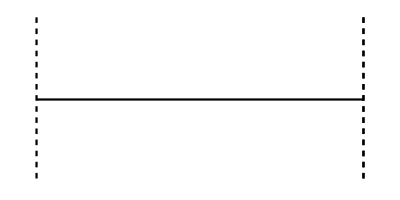

```mathematica
MADDraw[testline]
```

### Optics Comparison

```mathematica
{betxi,alfxi,betyi,alfyi}={20,-2,2,0};
```

```mathematica
btstwissinitial:={MLCBetaGamma[betxi,alfxi],MLCBetaGamma[betyi,alfyi]};
```

```mathematica
btsdispinitial:={0,0,0,0,0,1};
```

```mathematica
MLCGenerateTwissTable[MADSplitElements[{testline},100],btstwissinitial,{0,0},btsdispinitial];
```

```mathematica
latticename="lattice"
```

lattice

```mathematica
MADWrite[latticename,testline,Slice->10]
```

```mathematica
MADWriteInitialConditions[latticename,"btsstart",betxi,alfxi,betyi,alfyi,0.0,0.0,0.0,0.0]
```

```mathematica
MADCreateOpticsData[latticename,0,"btsstart"]
```

```mathematica
MADSave[latticename,"savedfile.mff"]
```

```mathematica
RunMAD["lattice.mff"];
```

```mathematica
MADReadOpticsData[]
```

```mathematica
GAMX=Thread[(1+ALFX^2)/BETX];
```

```mathematica
GAMY=Thread[(1+ALFY^2)/BETY];
```

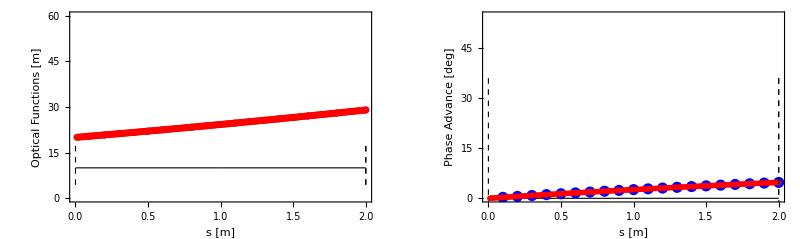

```mathematica
plot1=MADDraw[testline,Labels->False,Lengths->False,WidthScale->20,Thick->0.002,Bends->False,Offset->10,DisplayFunction->Identity];plot2=ListPlot[Transpose[{MLCS,MLCBETX}],DisplayFunction->Identity,Joined->False,PlotStyle->{Red,AbsolutePointSize[5]}];
plot3=ListPlot[Transpose[{S,BETX}],DisplayFunction->Identity,Joined->False,PlotStyle->{Blue,AbsolutePointSize[5]}];plota=Show[plot3,plot2,plot1,PlotRange->{{0,Last[MLCS]},{0,60}},Frame->True,DisplayFunction->Identity,BaseStyle->{FontFamily->"Times",FontSize->18},FrameLabel->{"s [m]","Optical Functions [m]"}];
plot4=MADDraw[testline,Labels->False,Lengths->False,WidthScale->100,Thick->0.002,Bends->False,Offset->0,DisplayFunction->Identity];plot5=ListPlot[Transpose[{MLCS,(360 MLCMUX)/(2 π)}],DisplayFunction->Identity,Joined->False,PlotStyle->{Red,AbsolutePointSize[4]}];
plot6=ListPlot[Transpose[{S,360 MUX}],DisplayFunction->Identity,Joined->False,PlotStyle->{Blue,AbsolutePointSize[8]}];plotb=Show[plot6,plot5,plot4,PlotRange->{{0,Last[MLCS]},{0,50+360 Max[{MLCMUX/(2 π),MUX}]}},Frame->True,DisplayFunction->Identity,BaseStyle->{FontFamily->"Times",FontSize->18},FrameLabel->{"s [m]","Phase Advance [deg]"}];
Show[GraphicsRow[{plota,plotb}],DisplayFunction->$DisplayFunction,ImageSize->800]
```